```mathematica
ResourceFunction["DarkMode"][False](*leave argument empty for Darkmode. Add False to switch it off.*)
```

## Introduction

Created: 28.06.2023 - Alampounti
Edited: 06.10.2023

The following notebook is a complementary notebook to the 2-tone analysis notebook.nb.
It attempts to understand a bit better the stream analysis that Marcos is performing. 
The following work requires that you load Mosquito 25/set 3 on the 2-tone analysis notebook.
You only need to run the file names as this is all this code needs to run.

## A mini stream analysis

### Getting our bearings

We start by trying to replicate some of Marcos’ plots.
He has been using a very specific segment of the amplitude. He breaks the stimulus in a total of 10 pieces, and he selected the 3rd ( I believe arbitrarily).
As my attempt is simply to reproduce, I do not question this at this stage. 
I simply extract the relevant nerve trace, and run a standard peak detection algorithm that we are also using for DPTracing.

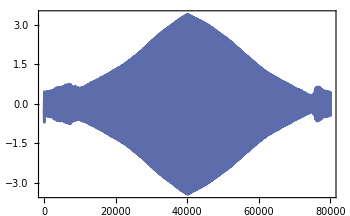

```mathematica
laser[[;;4 sRate]]//ListLinePlot
```

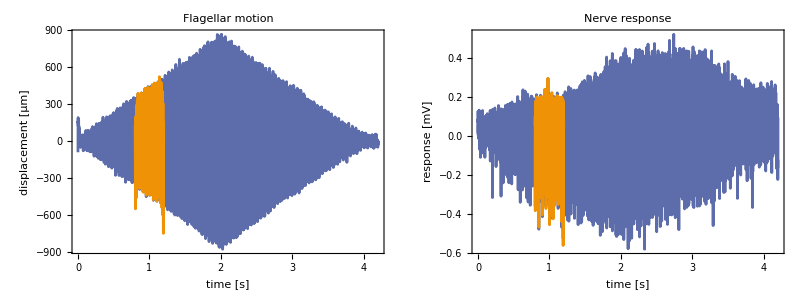

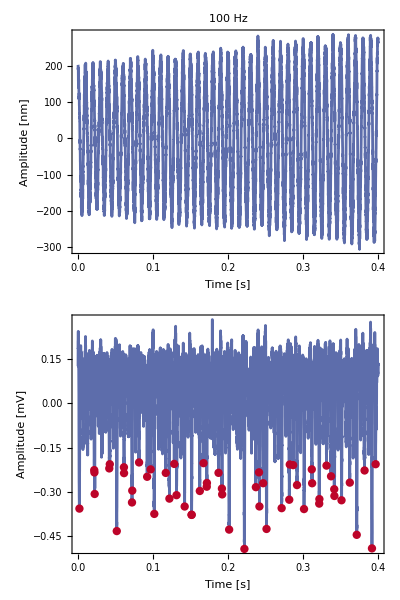

```mathematica
i=1;
st=16000; 
size=8000;
σNT=1.25;                                (* gaussian blurring to survive *)
peakSharpnessNT=0.002;  (* sharpness criterion *)
responseHeightNT=0.2; (* minimum peak height in nm *)
tL=Fold[HighpassFilter,readMyFile[laserfiles1T[[i]]][[;;,2]],(2π)/sRate{60,60,60}][[st;;st+size]]; (* extract the relevant laser trace *)
t=Fold[HighpassFilter,readMyFile[nervefiles1T[[i]]][[;;,2]],(2π)/sRate{60,60,60}][[st;;st+size]]; (* extract the relevant nerve trace *)
peaksT=FindPeaks[-t,σNT,peakSharpnessNT,responseHeightNT][[;;,1]]; (* find the peaks on the nerve *)


(* plotting the full flagellar and nerve responses and highlight the extracted part *)
Grid@{{ListLinePlot[{{Range[Length@readMyFile[laserfiles1T[[i]]][[;;,1]]][[;; ;;10]]/sRate,Fold[HighpassFilter,readMyFile[laserfiles1T[[i]]][[;;,2]][[;; ;;10]],(2π)/sRate{60,60,60}]}ᵀ,
{Range[Length@readMyFile[laserfiles1T[[i]]][[;;,1]]][[st;;st+size ;;10]]/sRate,Fold[HighpassFilter,readMyFile[laserfiles1T[[i]]][[;;,2]][[st;;st+size;;10]],(2π)/sRate{60,60,60}]}ᵀ},PlotLabel->"Flagellar motion",FrameLabel->{"time [s]","displacement [μm]"}], ListLinePlot[{{Range[Length@readMyFile[nervefiles1T[[i]]][[;;,1]]][[;; ;;10]]/sRate,Fold[HighpassFilter,readMyFile[nervefiles1T[[i]]][[;;,2]][[;; ;;10]],(2π)/sRate{60,60,60}]}ᵀ,
{Range[Length@readMyFile[nervefiles1T[[i]]][[;;,1]]][[st;;st+size ;;10]]/sRate,Fold[HighpassFilter,readMyFile[nervefiles1T[[i]]][[;;,2]][[st;;st+size;;10]],(2π)/sRate{60,60,60}]}ᵀ},PlotLabel->"Nerve response",FrameLabel->{"time [s]","response [mV]"}]}}
(* plotting the extracted laser trace *)
fig=Grid@{{ListLinePlot[{Range[Length@tL]/sRate,tL}ᵀ,FrameLabel->{"Time [s]","Amplitude [nm]"},Frame->{False,True,False,False},PlotLabel->ToString[freqs1T[[i]]]<>" Hz",ImageSize->800,AspectRatio->1/6]},

(* plotting the extracted nerve trace and indicate the detected peaks *)
{Show[{ListLinePlot[{(*{Range[Length@tL]/sRate,tL/1000}ᵀ,*){Range[Length@t]/sRate,t}ᵀ},FrameLabel->{"Time [s]","Amplitude [mV]"}(*,PlotLabel->ToString[freqs1T[[i]]]<>" Hz"*),ImageSize->800,AspectRatio->1/4],
ListPlot[{peaksT/sRate,t[[peaksT]]}ᵀ,PlotStyle->{red,AbsolutePointSize[6]}]}]}}
(*Export["C:\\Users\\hadif\\Dropbox\\Uni\\UCL\\Projects\\02_DP Theory paper\\DP concept paper\\images\\stream analysis\\fig."<>ToString[freqs1T[[i]]]<>".png",fig,ImageResolution->200];*)
```

Simply plotting the FFT of the extracted laser and nerve trace as well as the instantaneous frequency between the peaks.

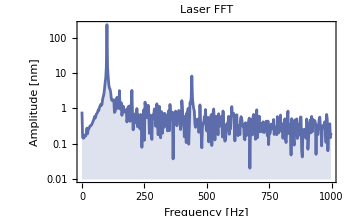
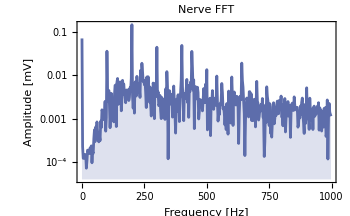
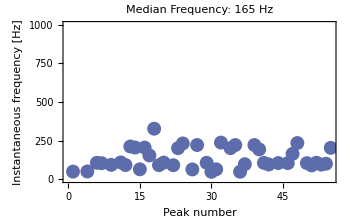
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
Grid@{{ListLinePlot[fourier[tL,sRate],ScalingFunctions->"Log",FrameLabel->{"Frequency [Hz]","Amplitude [nm]"},Filling->Bottom,FillingStyle->Automatic,PlotLabel->"Laser FFT"],SpanFromBoth},{ListLinePlot[fourier[t,sRate],ScalingFunctions->"Log",FrameLabel->{"Frequency [Hz]","Amplitude [mV]"},Filling->Bottom,PlotLabel->"Nerve FFT"],ListPlot[1.sRate/Differences[peaksT],PlotRange->{0,1000},FrameLabel->{"Peak number","Instantaneous frequency [Hz]"},PlotLabel->"Median Frequency: "<>ToString[Round[Median[1.sRate/Differences[peaksT]]]]<>" Hz"]}}
```

```mathematica
fourier[tL,sRate][[FindPeaks[fourier[tL,sRate][[;;,2]],0,0,100][[;;,1]]]]
fourier[t,sRate][[FindPeaks[fourier[t,sRate][[;;,2]],0,0,0.04][[;;,1]]]]
```

{{100.,214.985},{335.,398.475}}

{{0.,0.124538},{200.,0.126739},{235.,0.267473},{335.,0.0701629},{435.,0.216127},{470.,0.0562845},{535.,0.0473657},{635.,0.0479048},{670.,0.0943026}}

```mathematica
{F1,F3}={100,335};
quad=F3-F1;
Print["The quadratic is:",quad]
freqChoice=335;
Select[1.sRate/Differences[peaksT],freqChoice-5<=#<=freqChoice+5&];
Print["These are the frequencies that could be attributed to the quadratic:",%]
```

The quadratic is:235

These are the frequencies that could be attributed to the quadratic:{}

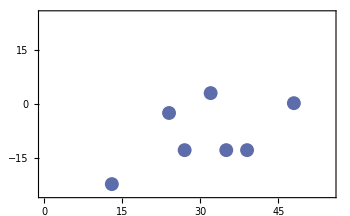

```mathematica
ListPlot[1.sRate/Differences[peaksT]-quad,PlotRange->{-25,25}] (* this plot show you where the spike rate lies relative to the quadratic *)
```

This is a histogram of the spike rates in the nerve. We can see that for a stimulus of 100 Hz, the vast majority of the spike rate is around 200 Hz.
This is well explained by a frequency doubled component of the stimulus.

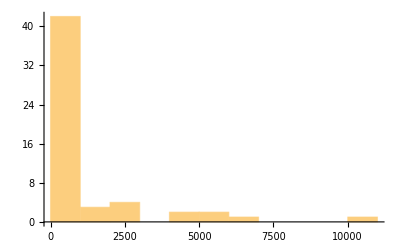

```mathematica
Histogram[1.sRate/Differences[peaksT],Automatic]
```

```mathematica
Sort/*Median@(1.sRate/Differences[peaksT])
```

224.719

```mathematica
<<AlexTools`ALXTools`
```

### Generalising to all stimulation frequencies

We want to apply everything we have done so far but to all frequencies that we use as stimulus.
We can see that as we scan that particular amplitude section, there are essentially two major peaks: One around 220 Hz and one around 500 Hz.
It is possible that we can identify multiple peaks, each corresponding to multiple “neuronal units”

```mathematica
tt=Fold[HighpassFilter,readMyFile[#][[st;;st+size,2]],(2π)/sRate{60,60,60}]&/@nervefiles1T[[;;]]; (* clean and extract the relevant segment for all 1-tone stimuli *)
peaksTT=FindPeaks[-#,σNT,peakSharpnessNT,responseHeightNT][[;;,1]]&/@tt; (* find all the peaks for all the stimulated nerves. The negative sign is because FindPeaks is looking for PEAKS and not TROUGHS!*)
spikeRate=1.sRate/Differences[#]&/@peaksTT; (* finds the instantaneous frequency between two spikes*)
```

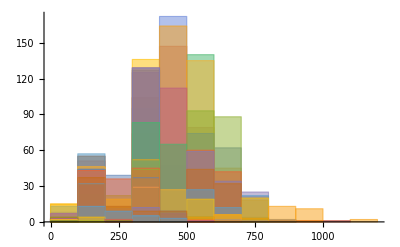

```mathematica
Histogram[spikeRate,PlotRange->Automatic] (* Plot ALL spikes generated across to see if there is a relative prevalance *)
```

```mathematica
Histogram3D[MapThread[Select[{1.sRate/Differences[#2],Table[#1,{i,Length@#2-1}]}ᵀ,#[[1]]<=1200&]&,{freqs1T[[;;]],peaksTT}],AxesLabel->{"Instantaneous nerve spike frequency [Hz]","Stimulus Frequency [Hz]","Counts [arb]"},AxesStyle->Directive[Black, 14]]
```

-Graphics3D-

NOTE: Although you cannot appreciate it, each ROW is a different colour. It is just due to the transparency properties of the 3D plot that you see this mixing of colours.
You can prove that each row is a unique colour by zooming in:

```mathematica
Histogram3D[MapThread[Select[{1.sRate/Differences[#2],Table[#1,{i,Length@#2-1}]}ᵀ,#[[1]]<=1200&]&,{freqs1T[[;;]],peaksTT}][[;;20]],AxesLabel->{"Instantaneous nerve spike frequency [Hz]","Stimulus Frequency [Hz]","Counts [arb]"},AxesStyle->Directive[ 14]]
```

-Graphics3D-

Can I extract the “typical” spike rate that is dominating the Histogram?
By sorting the data and then taking the Median, I am effectively extracting the Histogram Peak.

```mathematica
HistogramList[spikeRate[[1]],200]
```

Part::partd: Part specification spikeRate⟦1⟧ is longer than depth of object.

HistogramList::ldata: spikeRate⟦1⟧ is not a valid dataset or list of datasets.

HistogramList[spikeRate⟦1⟧,200]

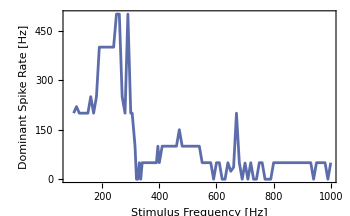

```mathematica
bin=100;
ListLinePlot[Table[{freqs1T[[i]],1.Select[(Select[{HistogramList[spikeRate[[i]],bin][[1,;;-2]],
HistogramList[spikeRate[[i]],bin][[2]]}ᵀ,#[[1]]<=600&]/.{}->{∅}),#[[2]]==Max[HistogramList[spikeRate[[i]],bin][[2]]]&][[1,1]]}ᵀ,{i,1,Length@spikeRate}],
FrameLabel->{"Stimulus Frequency [Hz]","Dominant Spike Rate [Hz]"}]
```

224.719

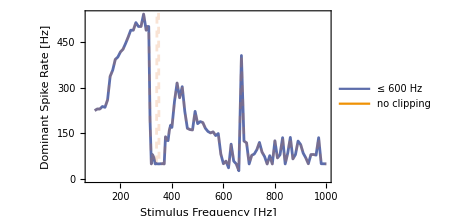

```mathematica
Sort/*Median@spikeRate[[1]] (* this is an example of us finding the dominant spike rate for a given amplitude and frequency *)
cuttoff=600; (*Spike rates above this value are not considered real. Empirically found.*)
medianSpikeRate={freqs1T,Sort/*Median@#&/@spikeRate}ᵀ;
Show[{ListLinePlot[Select[medianSpikeRate,#[[2]]<=cuttoff&],FrameLabel->{"Stimulus Frequency [Hz]","Dominant Spike Rate [Hz]"},Epilog->Inset[LineLegend[cols[[;;2]],{"≤ 600 Hz","no clipping"}],Scaled[{0.8,0.9}]]],
ListLinePlot[medianSpikeRate,PlotStyle->{Dashed,orange2,Opacity[0.2]}]}]
```

Use the following to check the slope between any two points.

```mathematica
{{96.77964610461619,225.47187622233264},{142.4771499897821,233.8263837388888}}
(%[[2,2]]-%[[1,2]])/(%[[2,1]]-%[[1,1]])
```

{{96.7796,225.472},{142.477,233.826}}

0.182822

```mathematica
Manipulate[Grid@{{ListPlot[{{Range[Length@tt[[i]]]/sRate,tt[[i]]}ᵀ,{peaksTT[[i]]/sRate,tt[[i,peaksTT[[i]]]]}ᵀ},Joined->{True,False},AspectRatio->1/8,ImageSize->1000,PlotLabel->Style["Stimulus Frequency: "<>ToString[freqs1T[[i]]]<>" Hz \n Response Frequency: "<>ToString[Round@medianSpikeRate[[i,2]]]<>" Hz",Black,16]],Histogram[spikeRate[[i]],100,BarOrigin->Bottom,ImageSize->200,PlotRange->{{0,1200},Automatic}]}},{{i,1},1,Length@tt,1},Paneled->False]
```

Part::partd: Part specification tt⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{1/20000,1/10000},tt⟦1⟧} cannot be transposed.

Part::partd: Part specification peaksTT⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression peaksTT⟦1⟧ cannot be used as a part specification.

Transpose::nmtx: The first two levels of {{0.00005,0.0001},tt⟦1⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Histogram::ldata: spikeRate⟦1⟧ is not a valid dataset or list of datasets.

Part::partd: Part specification tt⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{1/20000,1/10000},tt⟦1⟧} cannot be transposed.

Part::partd: Part specification peaksTT⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression peaksTT⟦1⟧ cannot be used as a part specification.

Transpose::nmtx: The first two levels of {{0.00005,0.0001},tt⟦1⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Histogram::ldata: spikeRate⟦1⟧ is not a valid dataset or list of datasets.

Part::partd: Part specification tt⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{1/20000,1/10000},tt⟦1⟧} cannot be transposed.

Part::partd: Part specification peaksTT⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression peaksTT⟦1⟧ cannot be used as a part specification.

Transpose::nmtx: The first two levels of {{0.00005,0.0001},tt⟦1⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Histogram::ldata: spikeRate⟦1⟧ is not a valid dataset or list of datasets.

Part::partd: Part specification tt[[1]] is longer than depth of object.

Transpose::nmtx: 
                               1      2
   The first two levels of {{-----, -----}, tt[[1]]} cannot be transposed.
                             sRate  sRate

Part::partd: Part specification peaksTT[[1]] is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

Part::pkspec1: The expression peaksTT[[1]]
     cannot be used as a part specification.

Transpose::nmtx: 
                               1    2.000000000000000
   The first two levels of {{-----, -----------------}, tt[[1]]}
                             sRate        sRate
     cannot be transposed.

Transpose::nmtx: 
                               1     2.
   The first two levels of {{-----, -----}, tt[[1]]} cannot be transposed.
                             sRate  sRate

General::stop: Further output of Transpose::nmtx
     will be suppressed during this calculation.

Histogram::ldata: spikeRate[[1]] is not a valid dataset or list of datasets.

```mathematica
ls355Hz={{0.060293919369898454,-0.22881249507816914},{0.08000202944362797,-0.23529282289005593},{0.10035630706075849,-0.26769446194949165},{0.12006441713448801,-0.26769446194949165},{0.13977252720821753,-0.3000961010089265},{0.16044988859704853,-0.26769446194949165},{0.180157998670778,-0.3195370844445877},{0.2001891925162081,-0.35841905131590934},{0.2202203863616381,-0.3324977400683613},{0.2405746639787686,-0.35841905131590934}};
1/Differences[ls355Hz[[;;,1]]]
```

{50.7405,49.1297,50.7405,50.7405,48.3621,50.7405,49.9221,49.9221,49.1297}

### Examining the amplitude dependency

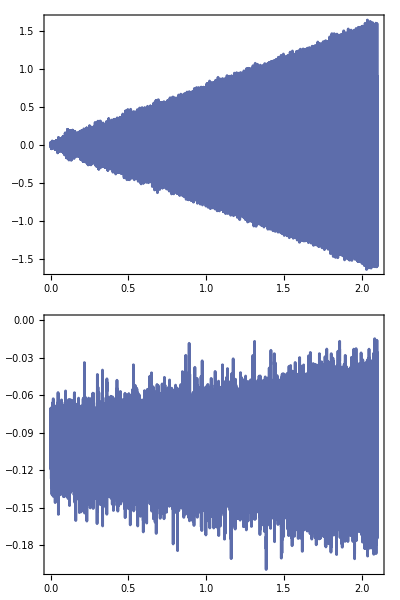

```mathematica
i=20;
laser=Fold[HighpassFilter,10^-3 readMyFile[laserfiles1T[[i]]][[;;,2]],(2π)/sRate{60,60,60}];
nerve=Fold[HighpassFilter,readMyFile[nervefiles1T[[i]]][[;;,2]],(2π)/sRate{60,60,60}];
Column[ListLinePlot[#[[;;sRate*2]],AspectRatio->1/4,ImageSize->600,DataRange->{0,Length@laser/2/sRate}]&/@{laser,nerve}]
```

Before we proceed I want to be able to visualise what I am doing. I start by partitioning the data.
There are some weird positive spikes in the nerve response. I do not fully understand it, but perhaps I don’t have to.

```mathematica
expDuration=4; (* seconds*)
numOfSegments=20; (* the number of segments I want to generate from the TOTAL nerve response - the full experimental duration  *)
size=expDuration sRate/numOfSegments (* number of samples per segment *)
```

4000

```mathematica
{laserfiles1TPS,laserfiles2TPS}=healthyFileFinder["\\Laser_PreStim","\\Signal_PreStim"];
{nervefiles1TPS,nervefiles2TPS}=healthyFileFinder["\\Nerve_PreStim","\\Signal_PreStim"];
```

Health check has been previously performed. Loading data from 'healthy_files' folder...

\Laser_PreStim channel's files have been analysed.
1-tone files: 84/101 are healthy.
2-tone files: 86/101 are healthy.

Health check has been previously performed. Loading data from 'healthy_files' folder...

\Nerve_PreStim channel's files have been analysed.
1-tone files: 84/101 are healthy.
2-tone files: 86/101 are healthy.

```mathematica
Clear[freqs,lfiles,nfiles,fLaser,fNerve]

tone=1;
tones={"1T","2T"};
{freqs,lfiles,nfiles}=ToExpression[#<>tones[[tone]]]&/@{"freqs","laserfiles","nervefiles"};; (* select whether you want to work with 1-tone or 2-tone data*)
freqs=ToExpression[freqs];
fLaser=Fold[HighpassFilter,readMyFile[#][[;;expDuration sRate,2]],(2π)/sRate{60,60,60}]&/@lfiles[[;;]]; (* applies a HPF to all laser data *)
fNerve=Fold[HighpassFilter,readMyFile[#][[;;expDuration sRate,2]],(2π)/sRate{60,60,60,60,60}]&/@nfiles[[;;]]; (* applies a HPF to all nerve data *)
```

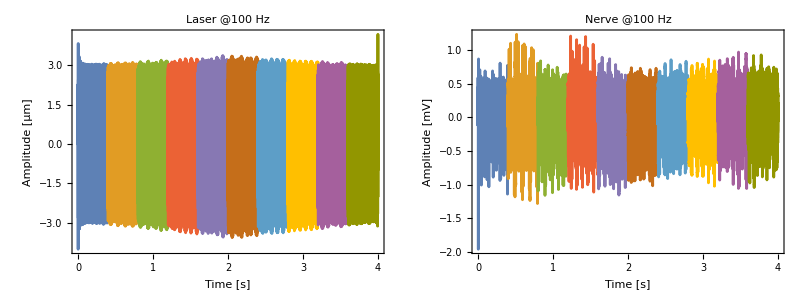

```mathematica
i=1;
laserExample={Range[Length@fLaser[[i]]]/sRate,10^-3 fLaser[[i]]}ᵀ;
nerveExample={Range[Length@fNerve[[i]]]/sRate,fNerve[[i]]}ᵀ;
Grid[{{ListLinePlot[Partition[laserExample,size],PlotStyle->ColorData[97],FrameLabel->{"Time [s]","Amplitude [μm]"},PlotLabel->"Laser @"<>ToString[freqs1T[[i]]]<>" Hz"],
ListLinePlot[Partition[nerveExample,size],PlotStyle->ColorData[97],FrameLabel->{"Time [s]","Amplitude [mV]"},PlotLabel->"Nerve @"<>ToString[freqs1T[[i]]]<>" Hz"]}}]
```

```mathematica
(*Grid@Partition[ListLinePlot[Partition[nerveExample,size][[#]],ImageSize->250,PlotStyle->ColorData[97,#],FrameTicks->{True,True}]&/@Range@numOfSegments,UpTo[4]]*)
```

```mathematica
ListLinePlot[Partition[nerveExample,size][[-2]][[600;;750,2]],Mesh->Full,PlotStyle->ColorData[97,9]]
```

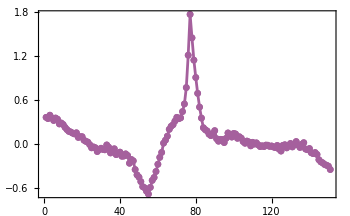

```mathematica
11./sRate 10^3
```

0.55

The upward ticks are rather sharp, and chances are they are not biologically relevant.

```mathematica
Clear[pLaser,pNerv,σNT,peakSharpnessNT,responseHeightNT,peaksNerve,spikeRateT,cuttoff,medianSpikeRateT]
pLaser=Partition[#,size]&/@fLaser; (*partitioned nerve data*)
pNerv=Partition[#,size]&/@fNerve; (*partitioned nerve data*)
```

```mathematica
σNT=1.25;                                (* gaussian blurring to survive. Originally 1.25 *)
peakSharpnessNT=0.002;  (* sharpness criterion *)
responseHeightNT=0.1; (* minimum peak height in nm - initially set at 0.2*)
peaksNerve=Parallelize@Table[FindPeaks[-pNerv[[freq,#]],σNT,peakSharpnessNT,responseHeightNT][[;;,1]]&/@Range[1,numOfSegments,1],{freq,1,Length@pNerv}];
```

```mathematica
spikeRateT=Table[1.sRate/Differences[#]&/@peaksNerve[[;;,seg]],{seg,1,numOfSegments}];
cuttoff=600; (*Spike rates above this value are not considered real. Empirically found.*)
medianSpikeRateT=Table[{freqs,Sort/*Median@#&/@spikeRateT[[seg]]}ᵀ,{seg,1,numOfSegments}];
```

```mathematica
plotUpperRange=2400;
phaseThreshold=0.04; (* what is the minimum FFT peak amplitude for the phase to be calculated? *)
Manipulate[Grid[{{ListPlot[{pNerv[[freq,seg]],{peaksNerve[[freq,seg]],pNerv[[freq,seg]][[peaksNerve[[freq,seg]]]]}ᵀ},Joined->{True,False},AspectRatio->1/8,ImageSize->1000,PlotLabel->"Stim Freq: "<>ToString[freqs[[freq]]]<>" Hz\n Median spike rate: "<>ToString[Round@medianSpikeRateT[[seg,freq,2]]]<>" Hz \n Segment No: "<>ToString[seg]<>" of "<>ToString[numOfSegments],FrameLabel->{"samples / time","Amlitude [mV]"},PlotRange->{Full,Full}],SpanFromLeft},
(* Laser FFT*)
{ListLogPlot[fourier[pLaser[[freq,seg]],sRate,1200],Joined->True,PlotStyle->red,AspectRatio->1/2,GridLines->{(freqs[[freq]]{1,2,3})~Join~{{540,Orange}}, None},FrameLabel->{"Frequency [Hz]","Amlitude [nm]"}],
(* Nerve FFT *)
ListLinePlot[fourier[pNerv[[freq,seg]],sRate,1200],Joined->True,PlotStyle->blue,AspectRatio->1/2,FrameLabel->{"Frequency [Hz]","Amlitude [mV]"},GridLines->{(freqs[[freq]]{1,2,3})~Join~{{540,Orange}}, None}],
(* spike rates*)
ListPlot[{peaksNerve[[freq,seg]][[2;;]],spikeRateT[[seg,freq]]}ᵀ,AspectRatio->1/2,PlotRange->{0,plotUpperRange},GridLines->{ None,freqs[[freq]]{1,2,3}}],
Histogram[spikeRateT[[seg,freq]],100,BarOrigin->Left,PlotRange->{{0,200},{0,plotUpperRange}},ImageSize->300]},

{SpanFromAbove,ListLinePlot[fourier[pNerv[[freq,seg]],sRate,1200,phaseThreshold,"ϕ"],Joined->True,PlotStyle->green,AspectRatio->1/2,FrameLabel->{"Frequency [Hz]","Phase [°]"},GridLines->{freqs[[freq]]{1,2,3}, None},PlotRange->Full],SpanFromAbove}}],

{{freq,13},1,Length@pNerv,1},{{seg,3},1,numOfSegments,1},Paneled->False]
```

Part::partd: Part specification pNerv[[13,3]] is longer than depth of object.

Part::partd: Part specification peaksNerve[[13,3]]
     is longer than depth of object.

Part::partd: Part specification pNerv[[13,3]] is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

Part::pkspec1: The expression peaksNerve[[13,3]]
     cannot be used as a part specification.

ListLogPlot::lpn: 
   AlexTools`ALXFourier`fourier[pLaser[[13,3]], sRate, 1200.000000000000]
     is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: 
   AlexTools`ALXFourier`fourier[pNerv[[13,3]], sRate, 1200.000000000000]
     is not a list of numbers or pairs of numbers.

General::prng: Value of option PlotRange -> {0, plotUpperRange}
     is not All, Full, Automatic, a positive machine number, or an appropriate
     list of range specifications.

Histogram::ldata: 
   spikeRateT[[3,13]] is not a valid dataset or list of datasets.

ListLinePlot::lpn: 
   AlexTools`ALXFourier`fourier[pNerv[[13,3]], sRate, 1200.000000000000, 
     phaseThreshold, ϕ] is not a list of numbers or pairs of numbers.

Part::partd: Part specification peaksNerve⟦13,3⟧ is longer than depth of object.

Part::pkspec1: The expression peaksNerve⟦13,3⟧ cannot be used as a part specification.

Part::partd: Part specification medianSpikeRateT⟦3,13,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression peaksNerve⟦13,3⟧ cannot be used as a part specification.

General::prng: Value of option PlotRange -> {0,plotUpperRange} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Histogram::ldata: spikeRateT⟦3,13⟧ is not a valid dataset or list of datasets.

Threshold::method: Method "phaseThreshold" is not a valid method.

```mathematica
810-540 s
```

270

```mathematica
D[v[t]*v[t],t]
```

2 v[t] v'[t]

```mathematica
DPFinder[{f1,f2},4,True]/.{f1->800,f2->540}
```

{{{820,-820,2420},{-520,520,2680},{-1860,1860,2940}}}

```mathematica
Manipulate[ListPlot[{pNerv[[freq,seg]](*,{peaksNerve[[freq,seg]],pNerv[[freq,seg]][[peaksNerve[[freq,seg]]]]}ᵀ*),1 10^-3 pLaser[[freq,seg]]},Joined->{True,True},AspectRatio->1/8,ImageSize->1000,PlotLabel->"Stim Freq: "<>ToString[freqs[[freq]]]<>" Hz\n Median spike rate: "<>ToString[Round@medianSpikeRateT[[seg,freq,2]]]<>" Hz \n Segment No: "<>ToString[seg]<>" of "<>ToString[numOfSegments],FrameLabel->{"samples / time","Amlitude [mV]"},PlotRange->{Full,Full}],

{{freq,13},1,Length@pNerv,1},{{seg,3},1,numOfSegments,1},Paneled->False]
```

Part::partd: Part specification medianSpikeRateT⟦1,39,2⟧ is longer than depth of object.

Part::partd: Part specification pNerv[[39,1]] is longer than depth of object.

Part::partd: Part specification pLaser[[39,1]] is longer than depth of object.

Part::partd: Part specification freqs[[39]] is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

#### Can we reconstruct the spike rate pattern?

The following is trying to reconstruct stimulus 170 Hz, segment 3 for Mosquito 25 set 3.
You can add or remove some of the terms. These have been extracted by looking at the FFT freq and phase as shown above.

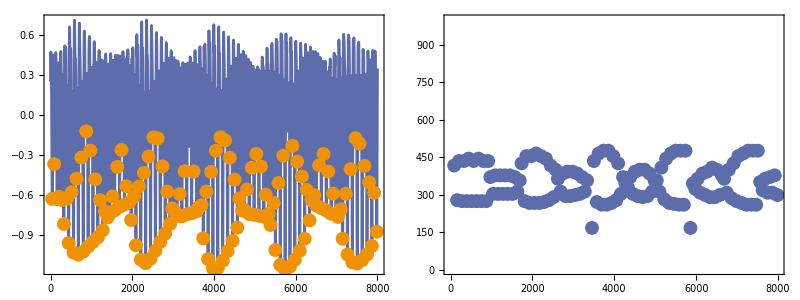

```mathematica
testingPeaks=Table[0.212Cos[(2π 158)/sRate t+85°]+0.156Cos[(2π 170)/sRate t-52.6°]+0.072Cos[(2π 182)/sRate t-148°]+0.08Cos[(2π 328)/sRate t-152°]+0.45Cos[(2π 340)/sRate t-47.6°]+0.216Cos[(2π 498)/sRate t-163°]+0.08Cos[(2π 510)/sRate t+66°]+0.07Cos[(2π 522)/sRate t-6.4°]+0.065Cos[(2π 658)/sRate t-95°]+0.057Cos[(2π 668)/sRate t-41°]+0.058Cos[(2π 680)/sRate t+96°]+0.05Cos[(2π 838)/sRate t-40°],{t,0,8000}];
testingFindingPeaks=FindPeaks[-testingPeaks,σNT,peakSharpnessNT,responseHeightNT][[;;,1]];
testingSpikeRate=1.sRate/Differences[testingFindingPeaks];
Grid@{{ListPlot[{testingPeaks,{testingFindingPeaks,testingPeaks[[testingFindingPeaks]]}ᵀ},AspectRatio->1/8,ImageSize->1000,Joined->{True,False}],ListPlot[{testingFindingPeaks[[2;;]],testingSpikeRate}ᵀ,AspectRatio->1/2,PlotRange->{0,plotUpperRange}]}}
```

I would conclude that we can fairly faithfully reproduce these patterns from the usage of the FFT alone.
Frequencies as high as 800 Hz are necessary here. But how many of them are PHYSICALLY relevant?

Let us try a more difficult version. let us look at the 220 Hz seg 3 case.

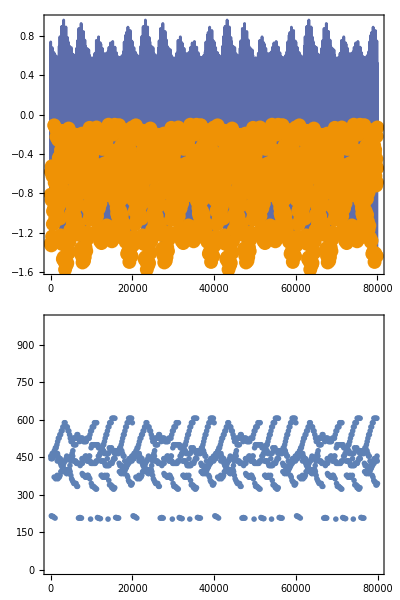

```mathematica
amps={0.166,0.049,0.1,0.186,0.106,0.116,0.066,0.478,0.242,0.099,0.101,0.064,0.056,0.079,0.051};(* these were hand-selected *)
freqs={108,150,215,220,328,332,435,440,548,655,660,768,772,880,988}; (* these were hand-selected *)
phases={-133,42,-117,-170,-140,147,-120,-65,3,47,-59,-3,-107,42,125};(* these were hand-selected *)

(* I would change the number of points to suit my needs. For individual settings I would do 8000 points, but if I want to see the larger structure I would do 24, 40 or even 80k *)
testingPeaks=Table[Evaluate[Total[#[[1]] Cos[(2π)/sRate #[[2]] x - #[[3]]°]&/@Select[({amps,freqs,phases}ᵀ),#[[1]]>=0.01&& Not@MemberQ[{},#[[2]]]&]]],{x,0,24000}]; (* you can raise the threshold here or remove frequencies *)
testingFindingPeaks=FindPeaks[-testingPeaks,σNT,peakSharpnessNT,responseHeightNT][[;;,1]];
testingSpikeRate=1.sRate/Differences[testingFindingPeaks];
Grid@{{ListPlot[{testingPeaks,{testingFindingPeaks,testingPeaks[[testingFindingPeaks]]}ᵀ},AspectRatio->1/8,ImageSize->1000,Joined->{True,False}]},{ListPlot[{testingFindingPeaks[[2;;]],testingSpikeRate}ᵀ,AspectRatio->1/8,PlotRange->{0,plotUpperRange},PlotStyle->AbsolutePointSize[4],ImageSize->1000]}}
```

#### Can we understand why we can see the fundamental tone in the nerve despite frequency doubling?

I want to understand how come we can still see the fundamental if frequency doubling is there. 
It should be invisible, no?

{{2024,240.964},{2694,229.885},{2940,240.964},{3364,222.222},{3610,232.558},{3856,243.902}}

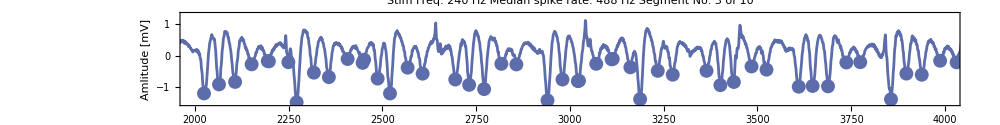

```mathematica
{freq,seg}={15,3};
maxFreq=300;
peaksOfInterest=Select[{peaksNerve[[freq,seg]][[2;;]],1.sRate/Differences[peaksNerve[[freq,seg]]]}ᵀ,pltRange[[1]]<=#[[1]]<=pltRange[[2]]&&#[[2]]<=maxFreq &]
pltRange={2000,4000};
Show[{ListPlot[{pNerv[[freq,seg]]},Joined->{True,False},AspectRatio->1/8,ImageSize->1000,PlotLabel->"Stim Freq: "<>ToString[freqs1T[[freq]]]<>" Hz\n Median spike rate: "<>ToString[Round@medianSpikeRateT[[seg,freq,2]]]<>" Hz \n Segment No: "<>ToString[seg]<>" of "<>ToString[numOfSegments],FrameLabel->{"samples / time","Amlitude [mV]"},PlotRange->{pltRange,Full},Joined->{True,False}(*,PlotHighlighting->Red*)],
ListPlot[{peaksNerve[[freq,seg]],pNerv[[freq,seg]][[peaksNerve[[freq,seg]]]]}ᵀ]}]
```

```mathematica
Manipulate[Grid@{{ListPlot[Table[{(peaksNerve[[freq,i]][[2;;]]+size (i-1))/sRate,spikeRateT[[i,freq]]}ᵀ,{i,1,10}],PlotRange->{0,1200},AspectRatio->1/8,ImageSize->1200,PlotStyle->{AbsolutePointSize[7]},PlotLabel->"Stimulus Frequency: "<>ToString[freqs[[freq]]]<>" Hz",FrameLabel->{"time [s]","instantaneous spike frequency [Hz]"},GridLines->{ None,freqs[[freq]]{1,2,3}}]},
{ListPlot[List/@Table[{ i,Length@spikeRateT[[i,freq]]}ᵀ,{i,1,numOfSegments}],AspectRatio->1/16,ImageSize->1200,PlotStyle->{AbsolutePointSize[7]},PlotRange->{0,150},FrameLabel->{"segment number","spike count"}]}},{{freq,13},1,Length@peaksNerve,1},Paneled->False]
```

Part::partd: Part specification peaksNerve[[82,1]]
     is longer than depth of object.

Part::partd: Part specification 82[[1]] is longer than depth of object.

Part::partd: Part specification spikeRateT[[1,82]]
     is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

Table::iterb: Iterator {i, 1, numOfSegments} does not have appropriate bounds.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1
     will be suppressed during this calculation.

```mathematica
Manipulate[Histogram[Select[Flatten[spikeRateT[[;;,freq]]],#<5000&],50,PlotRange->{{0,2000},{0,1500}},GridLines->{ freqs[[freq]]{1,2,3,4,5},None},PlotLabel->ToString[freqs1T[[freq]]]<>" Hz"],{freq,1,Length@freqs1T,1},Paneled->False]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partd: Part specification freqs[[1]] is longer than depth of object.

Part::partd: Part specification freqs1T[[1]] is longer than depth of object.

Histogram::ldata: Symbol[] is not a valid dataset or list of datasets.

```mathematica
Manipulate[Histogram[Table[Select[spikes,#<5000&],{spikes,spikeRateT[[;;,freq]]}],50,PlotRange->{{0,20000},{0,150}},GridLines->{ freqs[[freq]]{1,2,3,4,5},None},PlotLabel->ToString[freqs1T[[freq]]]<>" Hz"],{freq,1,Length@freqs1T,1},Paneled->False]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Table::iterb: Iterator {spikes, Symbol[]} does not have appropriate bounds.

Part::partd: Part specification freqs[[1]] is longer than depth of object.

Part::partd: Part specification freqs1T[[1]] is longer than depth of object.

Histogram::ldata: 
   Table[Select[spikes, #1 < 5000 & ], {spikes, Symbol[]}]
     is not a valid dataset or list of datasets.

### Spike Counts

```mathematica
segs=numOfSegments/2;
ListLinePlot3D[Table[{ freqs[[j]],i,Length@spikeRateT[[i,j]]}ᵀ,{i,1,segs},{j,1,Length@freqs}],Filling->Bottom,PlotTheme->"Default",ImageSize->600(*,AxesStyle->{LightGray,16},TicksStyle->Directive[LightGray, 14]*)]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{ freqs[[j]],i,Length@spikeRateT[[i,j]]}ᵀ,{i,1,numOfSegments},{j,1,Length@freqs}],1],InterpolationOrder->1,PlotRange->{0,300},ColorFunction->color]
```

-Graphics3D-

```mathematica
(26.85+150+22.83)3+26.85+150
```

775.89

#### Can we understand which spike frequencies dominate a particular amplitude and frequency region?

This is done in a very dirty way: I simply sort and take the median of the spike rates and I plot that.

```mathematica
Manipulate[Show[{ListLinePlot[Select[medianSpikeRateT[[seg]],#[[2]]<=cuttoff&],FrameLabel->{"Stimulus Frequency [Hz]","Dominant Spike Rate [Hz]"},Epilog->Inset[LineLegend[cols[[;;2]],{"≤ 600 Hz","no clipping"}],Scaled[{0.8,0.9}]],PlotRange->{0,650}],
ListLinePlot[medianSpikeRateT[[seg]],PlotStyle->{Dashed,orange2,Opacity[0.2]}]}],{seg,1,numOfSegments,1},Paneled->False]
```

Part::partd: Part specification medianSpikeRateT⟦9⟧ is longer than depth of object.

Part::partd: Part specification medianSpikeRateT⟦2⟧ is longer than depth of object.

Part::partd: Part specification 9⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ListLinePlot::lpn: Part[] is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression 9 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLinePlot::lpn: medianSpikeRateT⟦9⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[Part[],FrameLabel→{Stimulus Frequency [Hz],Dominant Spike Rate [Hz]},Epilog→Inset[≤ 600 Hz,Scaled[{0.8,0.9}]],PlotRange→{0,650}],ListLinePlot[medianSpikeRateT⟦9⟧,PlotStyle→{Dashing[{Small,Small}],color,Opacity[0.2]}]}].

Part::partd: Part specification medianSpikeRateT⟦9⟧ is longer than depth of object.

Part::partd: Part specification medianSpikeRateT⟦2⟧ is longer than depth of object.

Part::partd: Part specification 9⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ListLinePlot::lpn: Part[] is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression 9 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLinePlot::lpn: medianSpikeRateT⟦9⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[Part[],FrameLabel→{Stimulus Frequency [Hz],Dominant Spike Rate [Hz]},Epilog→Inset[≤ 600 Hz,Scaled[{0.8,0.9}]],PlotRange→{0,650}],ListLinePlot[medianSpikeRateT⟦9⟧,PlotStyle→{Dashing[{Small,Small}],color,Opacity[0.2]}]}].

Part::partd: Part specification medianSpikeRateT[[9]]
     is longer than depth of object.

Part::partd: Part specification medianSpikeRateT[[2]]
     is longer than depth of object.

Part::partd: Part specification 9[[2]] is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::take: Cannot take positions 1 through 2 in AlexTools`ALXSettings`cols.

ListLinePlot::lpn: Part[] is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: 
   medianSpikeRateT[[9]] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in 
    Show[{ListLinePlot[Part[], FrameLabel -> 
        {Stimulus Frequency [Hz], Dominant Spike Rate [Hz]}, 
       Epilog -> Inset[LineLegend[<<26>>[[<<1>>]], <<1>>], <<1>>], 
       PlotRange -> {0, 650}], <<1>>}].

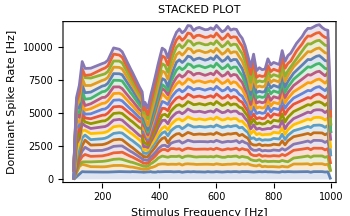

```mathematica
StackedListPlot[Select[#,#[[2]]<=cuttoff&]&/@medianSpikeRateT,Frame->{True,True,False,False},FrameLabel->{"Stimulus Frequency [Hz]","Dominant Spike Rate [Hz]"},PlotLabel->"STACKED PLOT"]
```

```mathematica
22.8/9
```

2.53333

```mathematica
ListLinePlot3D[Table[Insert[#,seg,2]&/@(Select[#,#[[2]]<=cuttoff&]&/@medianSpikeRateT)[[seg]],{seg,1,numOfSegments}],PlotTheme->"Marketing"(*,Mesh->Full,PlotStyle->Thin,PlotMarkers->{Automatic, Medium}*),AxesLabel->{"Stimulus Frequency [Hz]","Segment Slice","Dominant Freq. Response [Hz]"},ImageSize->800]
```

-Graphics3D-

### What is the spike amplitude as a function of freq & stimulus amplitude?

This uses the exact same code as peaksNerve, but rather than taking the positional argument I take the amplitude one. 
The bottom line that I would draw from this is that there is little I can say about the nerve response based on the amplitude alone.

```mathematica
peaksNerveAmp=Table[FindPeaks[-pNerv[[freq,#]],σNT,peakSharpnessNT,responseHeightNT][[;;,2]]&/@Range[1,numOfSegments,1],{freq,1,Length@pNerv}];
```

```mathematica
Manipulate[Grid@{{ListPlot[{pNerv[[freq,seg]],{peaksNerve[[freq,seg]],pNerv[[freq,seg]][[peaksNerve[[freq,seg]]]]}ᵀ},Joined->{True,False},AspectRatio->1/8,ImageSize->1000,PlotLabel->"Stim Freq: "<>ToString[freqs1T[[freq]]]<>" Hz \n Segment No: "<>ToString[seg]<>" of "<>ToString[numOfSegments]],Histogram[peaksNerveAmp[[freq,seg]],Automatic,BarOrigin->Bottom,ImageSize->200,PlotRange->{0,100}]}},{freq,1,Length@pNerv,1},{seg,1,numOfSegments,1},Paneled->False]
```

Part::partd: Part specification pNerv⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification peaksNerve⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification pNerv⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression peaksNerve⟦1,1⟧ cannot be used as a part specification.

Histogram::ldata: peaksNerveAmp⟦1,1⟧ is not a valid dataset or list of datasets.

Part::partd: Part specification peaksNerveAmp⟦1,1⟧ is longer than depth of object.

Histogram::ldata: peaksNerveAmp⟦1,1⟧ is not a valid dataset or list of datasets.

Part::partd: Part specification peaksNerveAmp⟦1,1⟧ is longer than depth of object.

Histogram::ldata: peaksNerveAmp⟦1,1⟧ is not a valid dataset or list of datasets.

Part::partd: Part specification peaksNerveAmp⟦1,1⟧ is longer than depth of object.

Histogram::ldata: peaksNerveAmp⟦1,1⟧ is not a valid dataset or list of datasets.

Part::partd: Part specification pNerv[[1,1]] is longer than depth of object.

Part::partd: Part specification peaksNerve[[1,1]]
     is longer than depth of object.

Part::partd: Part specification pNerv[[1,1]] is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

Part::pkspec1: The expression peaksNerve[[1,1]]
     cannot be used as a part specification.

Histogram::ldata: 
   peaksNerveAmp[[1,1]] is not a valid dataset or list of datasets.

```mathematica
seg=1;
Histogram3D[Table[MapThread[{#2,#1}&,{Table[freqs1T[[freq]],{i,Length@peaksNerveAmp[[freq,seg]]}],peaksNerveAmp[[freq,seg]]}],{freq,1,Length@freqs1T}],ChartElementFunction->"GradientScaleCube",ImageSize->500,PlotTheme->"Marketing",PlotLabel->"Segment: "<>ToString[seg]<>"/"<>ToString[numOfSegments],PlotRange->{{0,3},Automatic,Automatic},ViewPoint->Top]
```

-Graphics3D-

```mathematica
Grid@Partition[Histogram3D[Table[MapThread[{#2,#1}&,{Table[freqs1T[[freq]],{i,Length@peaksNerveAmp[[freq,#]]}],peaksNerveAmp[[freq,#]]}],{freq,1,Length@freqs1T}],ChartElementFunction->"GradientScaleCube",ImageSize->300,PlotTheme->"Marketing",PlotLabel->"Segment: "<>ToString[#]<>"/"<>ToString[numOfSegments],PlotRange->{{0,1.2},Automatic,Automatic},ViewPoint->Top]&/@Range[numOfSegments],UpTo[5]]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

The following is just an image for the sake of preserving resources. The above function simply tries to see if there is any correlation between the spike amplitude and the frequency or amplitude of the stimulus.
The short answer is “probably no”.

### Reconstructing the 2-tone stimulus that Marcos is working on

Marcos has been working on better understanding the 2-tone stimuli in the nerve.
Marcos had made the claim that he can reproduce the nerve response using just the 220 and 200 Hz frequencies.
The following code helped to show that his code had an error. He is currently working with this particular file:

```mathematica
st=8000; 
size=8000;
σNT=1.25;                                (* gaussian blurring to survive *)
peakSharpnessNT=0.002;  (* sharpness criterion *)
responseHeightNT=0.2; (* minimum peak height in nm *)
tL=Fold[HighpassFilter,readMyFile["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito25\\set_3\\Laser\\unhealthy_files\\M_AGA_Kisumu_ZT11_2023-02-14_No 001_Laser_b_025_(050).txt",2],(2π)/sRate{60,60,60}][[st;;st+size]]; (* extract the relevant laser trace *)
(* find the peaks on the nerve *)
tN=Fold[HighpassFilter,readMyFile["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito25\\set_3\\Nerve\\unhealthy_files\\M_AGA_Kisumu_ZT11_2023-02-14_No 001_Nerve_b_025_(050).txt",2],(2π)/sRate{60,60,60}][[st;;st+size]]; (* extract the relevant nerve trace *)
peaksT=FindPeaks[-tN,σNT,peakSharpnessNT,responseHeightNT][[;;,1]];
```

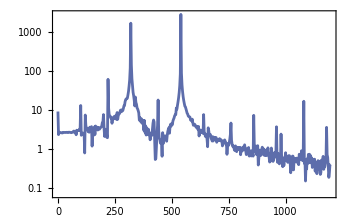

```mathematica
ListLogPlot[fourier[tL,sRate,1200],Joined->True]
```

A few things to notice: The file is considered “unhealthy” as far as the analysis is concerned, but let’s move on from here.

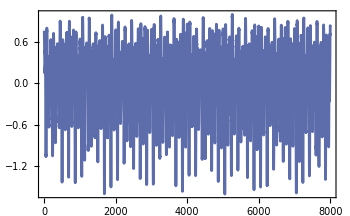
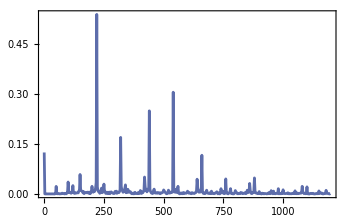

```mathematica
{{ListLinePlot[tN],
ListLinePlot[fourier[tN,sRate,1200]]}}
```

Here I am trying to reproduce Marcos’ V-shaped spike rates:
-Graphics-

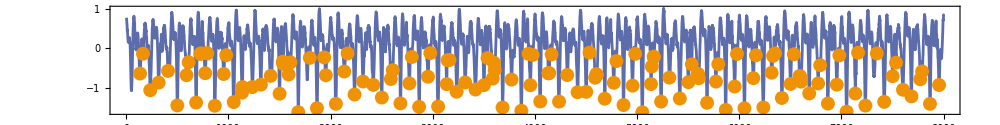

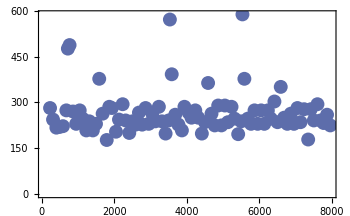

```mathematica
ppN=FindPeaks[-tN,1 (* gaussian blurring *),0.01 (* peak sharpness (2nd derivative) *),0.1 (* peak height *)][[;;,1]]; (* I find that the pattern is highly dependent on the peak finding parameters *)
ssN=1.sRate/Differences[ppN];
ListPlot[{tN,{ppN,tN[[ppN]]}ᵀ},Joined->{True,False},ImageSize->1000,AspectRatio->1/8]
ListPlot[Select[{ppN[[2;;]],ssN}ᵀ,#[[2]]<=600&]]
```

```mathematica
numOfPeaks=20; (* This will limit how many peaks will be considered as the most prominent ones. *)
peaksTest=FindPeaks[fourier[tN,sRate ,1200][[;;,2]],Automatic]; (* find all peaks up to 1200 Hz *)
prominentPeak=(Reverse@SortBy[fourier[tN,sRate,1200][[peaksTest[[;;,1]]]],Last])[[;;numOfPeaks]]; (* select the XXX most prominent peaks *)
%//TableForm
```

220. | 0.540109
540. | 0.306184
440. | 0.250108
320. | 0.170334
0. | 0.124969
660. | 0.116656
150. | 0.058778
420. | 0.0511128
880. | 0.0484703
760. | 0.0455043
640. | 0.0446491
100. | 0.0361313
860. | 0.0318977
250. | 0.0298822
340. | 0.0275633
120. | 0.0254278
560. | 0.0232904
200. | 0.0231945
1080. | 0.0231933
50. | 0.0230101

```mathematica
dps=Union@Flatten[DPFinder[{f1,f2},#,True]&/@Range[8]];
Select[dps/.{f1->320,f2->540},0<=#&];
observedDPs=Flatten[Table[Position[(dps/.{f1->320,f2->540}),Round[prominentPeak[[i,1]]]],{i,Length@prominentPeak}]];
TableForm[{dps[[observedDPs]],
obsFreqs=dps[[observedDPs]]/.{f1->320,f2->540}}ᵀ,TableHeadings->{None, {"DP","Frequency [Hz]"}}]
```

DP | Frequency [Hz]
-f1+f2 | 220
-2 f1+2 f2 | 440
-3 f1+3 f2 | 660
3 f1-f2 | 420
-4 f1+4 f2 | 880
-f1+2 f2 | 760
2 f1-f2 | 100
f1+f2 | 860
-4 f1+3 f2 | 340
-3 f1+2 f2 | 120
4 f1-2 f2 | 200

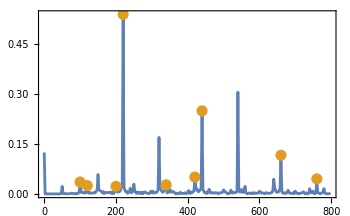
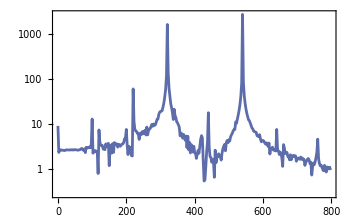

```mathematica
{ListLinePlot[{fourier[tN,sRate,800],fourier[tN,sRate,800][[Flatten[Position[fourier[tN,sRate,800][[;;,1]],1. #]&/@obsFreqs]]]},
Joined->{True,False},PlotStyle->{{Automatic},{Automatic,AbsolutePointSize[8]}}],ListLinePlot[{fourier[tL,sRate,800]},ScalingFunctions->"Log"]}
```

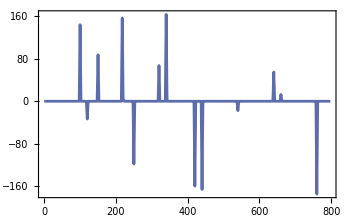
{-Graphics-,-Graphics-}

```mathematica
{ListLinePlot[{fourier[tN,sRate,800],fourier[tN,sRate,800][[Flatten[Position[fourier[tN,sRate,800][[;;,1]],1. #]&/@obsFreqs]]]},
Joined->{True,False},PlotStyle->{{Automatic},{Automatic,AbsolutePointSize[8]}}],ListLinePlot[fourier[tN,sRate,800,0.025,"ϕ"]]}
```

```mathematica
freqAndPhase=fourier[tN,sRate,1200,0.025,"ϕ"][[Flatten[Position[fourier[tN,sRate,1200,0.025,"ϕ"][[;;,1]],1. #]&/@obsFreqs]]];
frqAmp=fourier[tN,sRate,1200][[Flatten[Position[fourier[tN,sRate,1200][[;;,1]],1. #]&/@obsFreqs]]][[;;,2]];
allComponents=MapThread[Prepend[#2,#1]&,{frqAmp,freqAndPhase}];
```

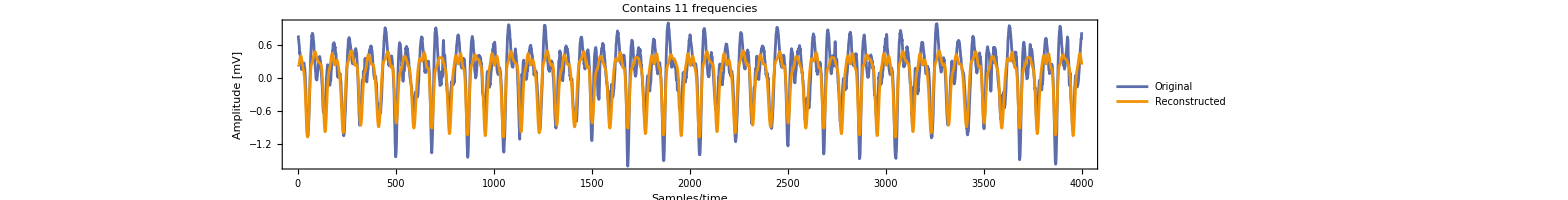

```mathematica
ListLinePlot[{tN[[;;4000]],Table[Total[#[[1]]Cos[(2π)/sRate#[[2]]t-#[[3]]°]&/@allComponents],{t,0,size/2}]},AspectRatio->1/6,ImageSize->1200,FrameLabel->{"Samples/time","Amplitude [mV]"},PlotLabel->"Contains "<>ToString[Length@observedDPs]<>" frequencies",PlotLegends->{"Original","Reconstructed"}]
```

```mathematica
Grid@{TableForm[{dps[[observedDPs]][[;;#]],Round[allComponents[[;;#,1]],1. 10^-3],obsFreqs[[;;#]],allComponents[[;;#,-1]]}ᵀ,TableHeadings->{None, {"DP","Amplitude [mV]","Freq. [Hz]","Phase [degrees °]"}}]&/@{10,5,2}}
```

DP | Amplitude [mV] | Freq. [Hz] | Phase [degrees °]
-f1+f2 | 0.567 | 220 | 23.8764
-2 f1+2 f2 | 0.269 | 440 | -134.387
-3 f1+3 f2 | 0.117 | 660 | 62.1769
3 f1-f2 | 0.072 | 420 | 112.434
-4 f1+4 f2 | 0.055 | 880 | -110.528
4 f1-2 f2 | 0.052 | 200 | -110.413
2 f1-f2 | 0.051 | 100 | 107.189
f1+f2 | 0.05 | 860 | -171.31
-f1+2 f2 | 0.043 | 760 | 153.151
-4 f1+3 f2 | 0.033 | 340 | -154.426 | DP | Amplitude [mV] | Freq. [Hz] | Phase [degrees °]
-f1+f2 | 0.567 | 220 | 23.8764
-2 f1+2 f2 | 0.269 | 440 | -134.387
-3 f1+3 f2 | 0.117 | 660 | 62.1769
3 f1-f2 | 0.072 | 420 | 112.434
-4 f1+4 f2 | 0.055 | 880 | -110.528 | DP | Amplitude [mV] | Freq. [Hz] | Phase [degrees °]
-f1+f2 | 0.567 | 220 | 23.8764
-2 f1+2 f2 | 0.269 | 440 | -134.387

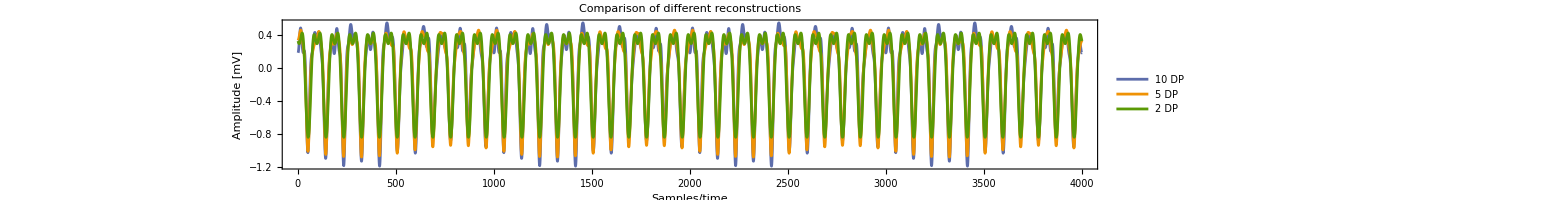

```mathematica
ListLinePlot[Table[Total[#[[1]]Cos[(2π)/sRate#[[2]]t-#[[3]]°]&/@allComponents[[;;component]]],{component,{10,5,2}},{t,0,size/2}],AspectRatio->1/6,ImageSize->1200,FrameLabel->{"Samples/time","Amplitude [mV]"},PlotLabel->"Comparison of different reconstructions",PlotLegends->{"10 DP","5 DP","2 DP"}]
```

```mathematica
fftMarcos={1. sRate/Length@tN Range[0,Length@tN-1],Abs[f=Fourier[tN,FourierParameters->{-1,1}]]}ᵀ;
```

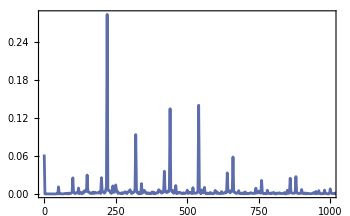

```mathematica
ListLinePlot[fftMarcos,PlotRange->{{0,1000},Full}]
```

```mathematica
nlmFit=NonlinearModelFit[tN,A1 Cos[(2π)/sRate 220 t+ϕ1]+A2 Cos[(2π)/sRate 440 t+ϕ2],{{A1,0.28},{A2,0.0258},ϕ1,ϕ2},t]
```

FittedModel[0.565812 Cos[0.520441-(11 π t)/500]+0.267553 Cos[14.7061+(11 π t)/250]]

```mathematica
ToExpression["A"<>ToString[i]]
```

```mathematica
Manipulate[Show[{ListLinePlot[tN[[;;2000]],AspectRatio->1/8,ImageSize->1000],
Plot[A1 Cos[(2π)/sRate 220 t-ϕ1 °]+A2 Cos[(2π)/sRate 440 t-ϕ2 °]+A3 Cos[(2π)/sRate 420 t-ϕ3 °]+A4 Cos[(2π)/sRate 200 t-ϕ4 °]+A5 Cos[(2π)/sRate 100 t-ϕ5 °]+A6 Cos[(2π)/sRate 340 t-ϕ6 °],{t,0,2000},PlotStyle->red]}],{{A1,0.567},0,1},{{A2,0.269},0,1},{{A3,0.072},0,1},{{A4,0.052},0,1},{{A5,0.051},0,1},{{A6,0.033},0,1},
{{ϕ1,24},-360,360},{{ϕ2,-134},-360,360},{{ϕ3,112},-360,360},{{ϕ4,-110},-360,360},{{ϕ5,107},-360,360},{{ϕ6,-154},-360,360},Paneled->False]
```

Part::take: Cannot take positions 1 through 2000 in tN.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression 1;;2000 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLinePlot::lpn: tN⟦1;;2000⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[tN⟦1;;2000⟧,AspectRatio→1/8,ImageSize→1000],}].

Part::take: Cannot take positions 1 through 2000 in tN.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression 1;;2000 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLinePlot::lpn: tN⟦1;;2000⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[tN⟦1;;2000⟧,AspectRatio→1/8,ImageSize→1000],}].

Part::take: Cannot take positions 1 through 2000 in tN.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression 1;;2000 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLinePlot::lpn: tN⟦1;;2000⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[tN⟦1;;2000⟧,AspectRatio→1/8,ImageSize→1000],}].

Part::take: Cannot take positions 1 through 2000 in tN.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression 1;;2000 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLinePlot::lpn: tN⟦1;;2000⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[tN⟦1;;2000⟧,AspectRatio→1/8,ImageSize→1000],}].

Part::take: Cannot take positions 1 through 2000 in tN.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: 
   tN[[1 ;; 2000]] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in 
                                                       1
    Show[{ListLinePlot[tN[[1 ;; 2000]], AspectRatio -> -, ImageSize -> 1000], 
                                                       8
      -Graphics-}].

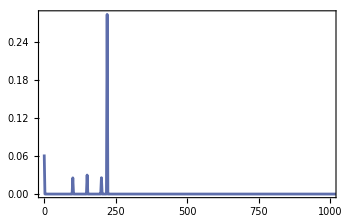

```mathematica
ListLinePlot[(fftMarcos/.{x_,y_}/;x>=300 ->{x,0})/.{x_,y_}/;y<=0.025 ->{x,0},PlotRange->{{0,1000},Full}]
```

```mathematica
Manipulate[Plot[{A1 Cos[(2π)/sRate f1 t-ϕ1 ],A2 Cos[(2π)/sRate f2 t-ϕ2 ],A1/2 Cos[(2π)/sRate f1 t-ϕ1 ]+A2/2 Cos[(2π)/sRate f2 t-ϕ2 ]},{t,200+timeSlide,4000+timeSlide},AspectRatio->1/8,ImageSize->1000],{{A1,1},0,1},{{A2,1},0,1},{{f1,200},180,300},{{f2,220},180,800},{{ϕ1,0},0,2π},{{ϕ2,0},0,2π},{timeSlide,0,10000},Paneled->False]
```

### What is the audibility region of the nerve?

And is it affected by the mechanical state of the animal or the stimulus amplitude?
We check this by looking the total area under the FFT curve for the nerve. We do this for all frequencies to give us an initial audiblity region.
We then repeat for all amplitude segments.

```mathematica
{nervefiles1TPS,nervefiles2TPS}=healthyFileFinder["\\Nerve_PreStim","\\Signal_PreStim"];
freqs1TPS=freqMap[#]&/@Sort@ToExpression[StringTake[nervefiles1TPS,{-8,-6}]]; (* frequencies of the one-tone experiments that made it past the health check *)
freqs2TPS=freqMap[#]&/@Sort@ToExpression[StringTake[nervefiles2TPS,{-8,-6}]];(* frequencies of the two-tone experiments that made it past the health check *)
```

Health check has been previously performed. Loading data from 'healthy_files' folder...

\Nerve_PreStim channel's files have been analysed.
1-tone files: 101/101 are healthy.
2-tone files: 101/101 are healthy.

```mathematica
audVals=Flatten[Position[freqs,#]&/@(freqs1TPS ∩freqs)]; (* These are the files for which we have a corresponding prestim*)
audValsPS=Flatten[Position[freqs1TPS,#]&/@(freqs1TPS ∩freqs)];
```

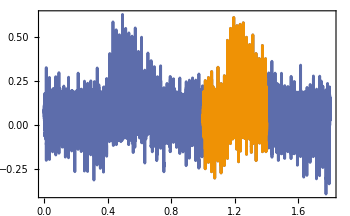

```mathematica
ListLinePlot[{{readMyFile[nervefiles1TPS[[audValsPS[[1]]]],1,2]-readMyFile[nervefiles1TPS[[audValsPS[[1]]]],1,2][[1]],Fold[HighpassFilter,readMyFile[nervefiles1TPS[[audValsPS[[1]]]],2,2],2π/sRate{60,60,60}]}ᵀ,{readMyFile[nervefiles1TPS[[audValsPS[[1]]]],1,2]-readMyFile[nervefiles1TPS[[audValsPS[[1]]]],1,2][[1]],Fold[HighpassFilter,readMyFile[nervefiles1TPS[[audValsPS[[1]]]],2,2],2π/sRate{60,60,60}]}ᵀ[[-2size;;-size]]}]
```

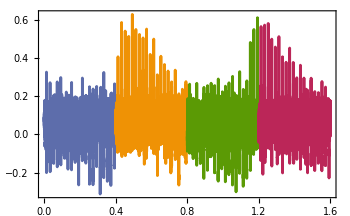

```mathematica
Partition[{readMyFile[nervefiles1TPS[[audValsPS[[1]]]],1,2]-readMyFile[nervefiles1TPS[[audValsPS[[1]]]],1,2][[1]],Fold[HighpassFilter,readMyFile[nervefiles1TPS[[audValsPS[[1]]]],2,2],2π/sRate{60,60,60}]}ᵀ,size]//ListLinePlot
```

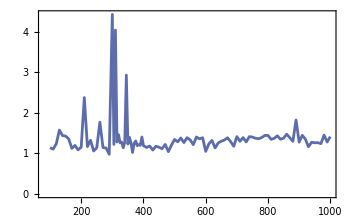

```mathematica
backgroundNPS={freqs1TPS[[#]],Total[fourier[Fold[HighpassFilter,readMyFile[nervefiles1TPS[[audValsPS[[#]]]],2,2],2π/sRate{60,60,60}][[-2size;;-size]],sRate,1200][[2;;,2]]]}&/@Range@Length@audVals;
ListLinePlot@%
```

```mathematica
averagedBackgroundNPS=Table[{freqs1TPS[[freq]],Mean[Total/@((fourier[#,sRate,1200]&/@Partition[Fold[HighpassFilter,readMyFile[nervefiles1TPS[[audValsPS[[freq]]]],2,2],2π/sRate{60,60,60}],size])[[;;,;;,2]])]},{freq,1,Length@audVals}];
```

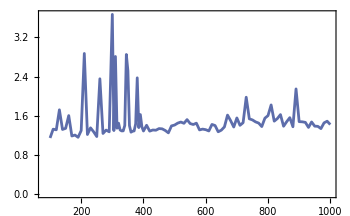

```mathematica
ListLinePlot[averagedBackgroundNPS]
```

```mathematica
-averagedBackgroundNPS[[1]]
```

{-100,-1.14541}

```mathematica
audibleRegion=Table[{freqs[[audVals[[freq]]]],amp,(Total@fourier[pNerv[[audVals[[freq]],amp]],sRate,1200][[;;,2]])-averagedBackgroundNPS[[freq,2]]}ᵀ,{amp,1,numOfSegments},{freq,1,Length@audVals}]; (* NOTE! IT is important that you select a prestimulus size that is EQUAL to your segment size. Otherwise you are comparing the spectral content of 2 seconds worth of nerve "exposure" to something close to 0.2 seconds of stimulated exposure. The background in those two cases will not be the same.*)
```

```mathematica
2 330 - 430
```

230

```mathematica
670- 330
```

340

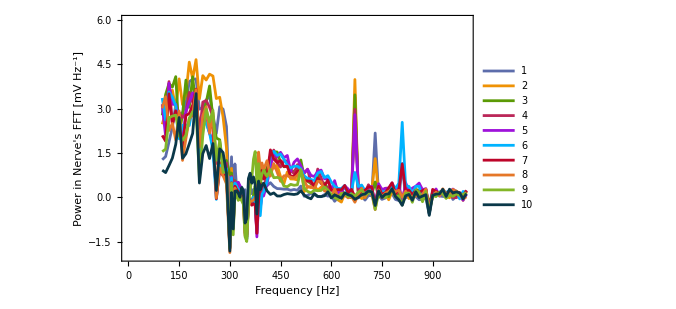
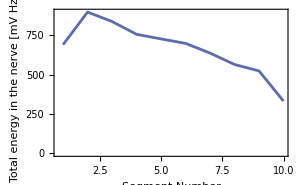
-Graphics- | -Graphics3D-
-Graphics- |

```mathematica
Grid@{{ListLinePlot[audibleRegion[[;;,;;,{1,3}]],PlotLegends->Range@numOfSegments,FrameLabel->{"Frequency [Hz]","Power in Nerve's FFT [mV Hz^-1]"},ImageSize->500,PlotRange->{-2,6}],
ListLinePlot3D[audibleRegion,PlotRange->Automatic,ImageSize->500,Filling->Axis,AxesLabel->{"Frequency [Hz]","Segment Number",Rotate["Power in Nerve [mV Hz^-1]",90°]},PlotTheme->"Detailed"]},
{ListLinePlot[Integrate[Interpolation[audibleRegion[[#,;;,{1,3}]]][t],{t,100,1000}]&/@Range[numOfSegments],FrameLabel->{"Segment Number","Total energy in the nerve [mV Hz^-2]"},ImageSize->300],SpanFromAbove}}
```

#### Where do the auditory neurons poise themselves on the saturation curve?

```mathematica
freqDesired=280;
illusInc=20; (* a downsampling of the data for illustrative purposes*)
chunkSize=0.1 sRate;
ilData={Range[Length@fLaser[[Position[freqs,freqDesired][[1,1]]]]]/sRate,fLaser[[Position[freqs,freqDesired][[1,1]]]]}ᵀ[[;;;;illusInc]]; (*illustrative data*)
Manipulate[Grid[{
{ListLinePlot[{ilData,ilData[[1+sRate *chunk/illusInc;;(sRate *chunk+chunkSize)/illusInc]]}]},

{ListLinePlot[fourier[fLaser[[Position[freqs,freqDesired][[1,1]],1+sRate *chunk;;sRate *chunk+chunkSize]],sRate,800],PlotLabel->"Flagellar Response",FrameLabel->{"Frequency [Hz]","Amplitude [nm]"}],
ListLinePlot[fourier[fNerve[[Position[freqs,freqDesired][[1,1]],1+sRate *chunk;;sRate *chunk+chunkSize]],sRate,800],PlotRange->{0,0.5},PlotLabel->"Nerve Response",FrameLabel->{"Frequency [Hz]","Amplitude [mV]"}(*,GridLines->{None, {0.295}}*)]}}],{chunk,0,2},Paneled->False]
```

Part::span: 1;;chunkSize/illusInc is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Fourier::fftl: Argument {{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, 589.276, 799.67, <<79986>>, -438.866, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]] is not a non-empty list or rectangular array of numeric quantities.

Part::take: Cannot take positions 1 through 2 in Abs[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, <<79989>>, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]].

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Fourier::fftl: Argument {{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, 589.276, 799.67, <<79986>>, -438.866, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]] is not a non-empty list or rectangular array of numeric quantities.

Part::take: Cannot take positions 1 through 2 in Abs[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, <<79989>>, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]].

Fourier::fftl: Argument {{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, 589.276, 799.67, <<79986>>, -438.866, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]] is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 2 in Arg[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, <<79989>>, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]].

General::stop: Further output of Part::take will be suppressed during this calculation.

Threshold::wlist: Argument 2 Abs[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, <<79990>>, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]][[1 ;; 2]] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0., 5000.}, 2 Abs[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, <<79992>>, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]][[1 ;; 2]]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

ListLinePlot::lpn: Transpose[] is not a list of numbers or pairs of numbers.

Part::partw: Part 1 of {} does not exist.

Threshold::wlist: Argument 2 Abs[Fourier[{{0.168056, 0.154895, 0.344687, 0.421629, 0.286517, 0.250644, <<79991>>, 0.121869, 0.115728, 0.131084}, <<93>>}[[<<2>>]], <<1>>]][[1 ;; 2]] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Transpose::nmtx: The first two levels of {{0., 5000.}, 2 Abs[Fourier[{{0.168056, 0.154895, 0.344687, 0.421629, 0.286517, <<79992>>, 0.121869, 0.115728, 0.131084}, <<93>>}[[<<2>>]], <<1>>]][[1 ;; 2]]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

ListLinePlot::lpn: Transpose[] is not a list of numbers or pairs of numbers.

Part::span: 1;;chunkSize/illusInc is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Fourier::fftl: Argument {{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, 589.276, 799.67, <<79986>>, -438.866, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]] is not a non-empty list or rectangular array of numeric quantities.

Part::take: Cannot take positions 1 through 2 in Abs[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, <<79989>>, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]].

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Fourier::fftl: Argument {{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, 589.276, 799.67, <<79986>>, -438.866, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]] is not a non-empty list or rectangular array of numeric quantities.

Part::take: Cannot take positions 1 through 2 in Abs[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, <<79989>>, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]].

Fourier::fftl: Argument {{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, 589.276, 799.67, <<79986>>, -438.866, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]] is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 2 in Arg[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, <<79989>>, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]].

General::stop: Further output of Part::take will be suppressed during this calculation.

Threshold::wlist: Argument 2 Abs[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, <<79990>>, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]][[1 ;; 2]] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0., 5000.}, 2 Abs[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, <<79992>>, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]][[1 ;; 2]]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

ListLinePlot::lpn: Transpose[] is not a list of numbers or pairs of numbers.

Part::partw: Part 1 of {} does not exist.

Threshold::wlist: Argument 2 Abs[Fourier[{{0.168056, 0.154895, 0.344687, 0.421629, 0.286517, 0.250644, <<79991>>, 0.121869, 0.115728, 0.131084}, <<93>>}[[<<2>>]], <<1>>]][[1 ;; 2]] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Transpose::nmtx: The first two levels of {{0., 5000.}, 2 Abs[Fourier[{{0.168056, 0.154895, 0.344687, 0.421629, 0.286517, <<79992>>, 0.121869, 0.115728, 0.131084}, <<93>>}[[<<2>>]], <<1>>]][[<<1>>]]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

ListLinePlot::lpn: Transpose[] is not a list of numbers or pairs of numbers.

Part::span: 1;;2000/illusInc is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: 1;;chunkSize/illusInc is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Fourier::fftl: Argument {{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, 589.276, 799.67, <<79986>>, -438.866, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]] is not a non-empty list or rectangular array of numeric quantities.

Part::take: Cannot take positions 1 through 2 in Abs[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, <<79989>>, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]].

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Fourier::fftl: Argument {{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, 589.276, 799.67, <<79986>>, -438.866, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]] is not a non-empty list or rectangular array of numeric quantities.

Part::take: Cannot take positions 1 through 2 in Abs[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, <<79989>>, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]].

Fourier::fftl: Argument {{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, 589.276, 799.67, <<79986>>, -438.866, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]] is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 2 in Arg[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, <<79989>>, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]].

General::stop: Further output of Part::take will be suppressed during this calculation.

Threshold::wlist: Argument 2 Abs[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, <<79990>>, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]][[1 ;; 2]] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0., 5000.}, 2 Abs[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, <<79992>>, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]][[1 ;; 2]]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

ListLinePlot::lpn: Transpose[] is not a list of numbers or pairs of numbers.

Part::partw: Part 1 of {} does not exist.

Threshold::wlist: Argument 2 Abs[Fourier[{{0.168056, 0.154895, 0.344687, 0.421629, 0.286517, 0.250644, <<79991>>, 0.121869, 0.115728, 0.131084}, <<93>>}[[<<2>>]], <<1>>]][[1 ;; 2]] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Transpose::nmtx: The first two levels of {{0., 5000.}, 2 Abs[Fourier[{{0.168056, 0.154895, 0.344687, 0.421629, 0.286517, <<79992>>, 0.121869, 0.115728, 0.131084}, <<93>>}[[<<2>>]], <<1>>]][[1 ;; 2]]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

ListLinePlot::lpn: Transpose[] is not a list of numbers or pairs of numbers.

Part::span: 1;;chunkSize/illusInc is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Fourier::fftl: Argument {{-46.2441, 0.689743, 48.8303, 139.078, 237.233, 398.697, 573.772, 776.16, 1006.56, <<79986>>, -517.039, -752.175, -905.85, -1004.88, -1018.17}, <<92>>}[[<<2>>]] is not a non-empty list or rectangular array of numeric quantities.

Part::take: Cannot take positions 1 through 2 in Abs[Fourier[{{-46.2441, 0.689743, 48.8303, 139.078, 237.233, 398.697, 573.772, <<79989>>, -752.175, -905.85, -1004.88, -1018.17}, <<92>>}[[<<2>>]], <<1>>]].

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Fourier::fftl: Argument {{-46.2441, 0.689743, 48.8303, 139.078, 237.233, 398.697, 573.772, 776.16, 1006.56, <<79986>>, -517.039, -752.175, -905.85, -1004.88, -1018.17}, <<92>>}[[<<2>>]] is not a non-empty list or rectangular array of numeric quantities.

Part::take: Cannot take positions 1 through 2 in Abs[Fourier[{{-46.2441, 0.689743, 48.8303, 139.078, 237.233, 398.697, 573.772, <<79989>>, -752.175, -905.85, -1004.88, -1018.17}, <<92>>}[[<<2>>]], <<1>>]].

Fourier::fftl: Argument {{-46.2441, 0.689743, 48.8303, 139.078, 237.233, 398.697, 573.772, 776.16, 1006.56, <<79986>>, -517.039, -752.175, -905.85, -1004.88, -1018.17}, <<92>>}[[<<2>>]] is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 2 in Arg[Fourier[{{-46.2441, 0.689743, 48.8303, 139.078, 237.233, 398.697, 573.772, <<79989>>, -752.175, -905.85, -1004.88, -1018.17}, <<92>>}[[<<2>>]], <<1>>]].

General::stop: Further output of Part::take will be suppressed during this calculation.

Threshold::wlist: Argument 2 Abs[Fourier[{{-46.2441, 0.689743, 48.8303, 139.078, 237.233, 398.697, 573.772, <<79990>>, -905.85, -1004.88, -1018.17}, <<92>>}[[<<2>>]], <<1>>]][[1 ;; 2]] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0., 5000.}, 2 Abs[Fourier[{{-46.2441, 0.689743, 48.8303, 139.078, 237.233, <<79992>>, -905.85, -1004.88, -1018.17}, <<92>>}[[<<2>>]], <<1>>]][[1 ;; 2]]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

ListLinePlot::lpn: Transpose[] is not a list of numbers or pairs of numbers.

Part::partw: Part 1 of {} does not exist.

Threshold::wlist: Argument 2 Abs[Fourier[{{0.159474, 0.213997, 0.444707, 0.590401, 0.502173, 0.429519, <<79991>>, 0.160688, 0.15413, 0.0927032}, <<92>>}[[<<2>>]], <<1>>]][[1 ;; 2]] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Transpose::nmtx: The first two levels of {{0., 5000.}, 2 Abs[Fourier[{{0.159474, 0.213997, 0.444707, 0.590401, 0.502173, <<79992>>, 0.160688, 0.15413, 0.0927032}, <<92>>}[[<<2>>]], <<1>>]][[1 ;; 2]]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

ListLinePlot::lpn: Transpose[] is not a list of numbers or pairs of numbers.

Part::span: 1;;chunkSize/illusInc is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Fourier::fftl: Argument fLaser⟦{}⟦1,1⟧,1;;chunkSize⟧ is not a non-empty list or rectangular array of numeric quantities.

Part::take: Cannot take positions 1 through 2 in Abs[Fourier[fLaser⟦{}⟦1,1⟧,1;;chunkSize⟧,FourierParameters→{-1,1}]].

Fourier::fftl: Argument fLaser⟦{}⟦1,1⟧,1;;chunkSize⟧ is not a non-empty list or rectangular array of numeric quantities.

Part::take: Cannot take positions 1 through 2 in Arg[Fourier[fLaser⟦{}⟦1,1⟧,1;;chunkSize⟧,FourierParameters→{-1,1}]].

Threshold::wlist: Argument 2 Abs[Fourier[fLaser⟦{}⟦1,1⟧,1;;chunkSize⟧,FourierParameters→{-1,1}]]⟦1;;2⟧ should be one of rectangular array of any depth, image, sound, or sampled sound list.

Transpose::nmtx: The first two levels of {{0.,5000.},2 Abs[Fourier[fLaser⟦{}⟦1,1⟧,1;;chunkSize⟧,FourierParameters→{-1,1}]]⟦1;;2⟧} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

ListLinePlot::lpn: Transpose[] is not a list of numbers or pairs of numbers.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Fourier::fftl: Argument fNerve⟦{}⟦1,1⟧,1;;chunkSize⟧ is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 2 in Abs[Fourier[fNerve⟦{}⟦1,1⟧,1;;chunkSize⟧,FourierParameters→{-1,1}]].

General::stop: Further output of Part::take will be suppressed during this calculation.

Threshold::wlist: Argument 2 Abs[Fourier[fNerve⟦{}⟦1,1⟧,1;;chunkSize⟧,FourierParameters→{-1,1}]]⟦1;;2⟧ should be one of rectangular array of any depth, image, sound, or sampled sound list.

Transpose::nmtx: The first two levels of {{0.,5000.},2 Abs[Fourier[fNerve⟦{}⟦1,1⟧,1;;chunkSize⟧,FourierParameters→{-1,1}]]⟦1;;2⟧} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

ListLinePlot::lpn: Transpose[] is not a list of numbers or pairs of numbers.

Part::span: 1;;chunkSize/illusInc is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Fourier::fftl: Argument {{23.5373, 21.1883, 39.4287, 81.557, 162.372, 273.575, 421.064, 612.742, 815.109, <<79986>>, -241.597, -480.853, -669.57, -793.359, -844.831}, <<90>>}[[<<2>>]] is not a non-empty list or rectangular array of numeric quantities.

Part::take: Cannot take positions 1 through 2 in Abs[Fourier[{{23.5373, 21.1883, 39.4287, 81.557, 162.372, 273.575, 421.064, <<7>>, <<79988>>, -480.853, -669.57, -793.359, -844.831}, <<90>>}[[<<2>>]], <<1>>]].

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Fourier::fftl: Argument {{23.5373, 21.1883, 39.4287, 81.557, 162.372, 273.575, 421.064, 612.742, 815.109, <<79986>>, -241.597, -480.853, -669.57, -793.359, -844.831}, <<90>>}[[<<2>>]] is not a non-empty list or rectangular array of numeric quantities.

Part::take: Cannot take positions 1 through 2 in Abs[Fourier[{{23.5373, 21.1883, 39.4287, 81.557, 162.372, 273.575, 421.064, <<7>>, <<79988>>, -480.853, -669.57, -793.359, -844.831}, <<90>>}[[<<2>>]], <<1>>]].

Fourier::fftl: Argument {{23.5373, 21.1883, 39.4287, 81.557, 162.372, 273.575, 421.064, 612.742, 815.109, <<79986>>, -241.597, -480.853, -669.57, -793.359, -844.831}, <<90>>}[[<<2>>]] is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 2 in Arg[Fourier[{{23.5373, 21.1883, 39.4287, 81.557, 162.372, 273.575, 421.064, <<7>>, <<79988>>, -480.853, -669.57, -793.359, -844.831}, <<90>>}[[<<2>>]], <<1>>]].

General::stop: Further output of Part::take will be suppressed during this calculation.

Threshold::wlist: Argument 2 Abs[Fourier[{{23.5373, 21.1883, 39.4287, 81.557, 162.372, 273.575, 421.064, <<79990>>, -669.57, -793.359, -844.831}, <<90>>}[[<<2>>]], <<1>>]][[1 ;; 2]] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0., 5000.}, 2 Abs[Fourier[{{23.5373, 21.1883, 39.4287, 81.557, 162.372, <<6>>5, <<79991>>, -669.57, -793.359, -844.831}, <<90>>}[[<<2>>]], <<1>>]][[<<1>>]]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

ListLinePlot::lpn: Transpose[] is not a list of numbers or pairs of numbers.

Part::partw: Part 1 of {} does not exist.

Threshold::wlist: Argument 2 Abs[Fourier[{{0.0488491, 0.0441294, 0.26982, 0.283415, 0.202413, 0.237309, <<79991>>, -0.0261172, 0.0206021, 0.0277067}, <<90>>}[[<<2>>]], <<1>>]][[1 ;; 2]] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Transpose::nmtx: The first two levels of {{0., 5000.}, 2 Abs[Fourier[{{0.0488491, 0.0441294, 0.26982, 0.283415, 0.202413, <<79992>>, <<10>>, 0.0206021, 0.0277067}, <<90>>}[[<<2>>]], <<1>>]][[<<1>>]]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

ListLinePlot::lpn: Transpose[] is not a list of numbers or pairs of numbers.

Part::span: 1;;chunkSize/illusInc is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Fourier::fftl: Argument {{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, 589.276, 799.67, <<79986>>, -438.866, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]] is not a non-empty list or rectangular array of numeric quantities.

Part::take: Cannot take positions 1 through 2 in Abs[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, <<79989>>, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]].

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Fourier::fftl: Argument {{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, 589.276, 799.67, <<79986>>, -438.866, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]] is not a non-empty list or rectangular array of numeric quantities.

Part::take: Cannot take positions 1 through 2 in Abs[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, <<79989>>, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]].

Fourier::fftl: Argument {{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, 589.276, 799.67, <<79986>>, -438.866, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]] is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 2 in Arg[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, <<79989>>, -687.345, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]].

General::stop: Further output of Part::take will be suppressed during this calculation.

Threshold::wlist: Argument 2 Abs[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, 264.461, 397.174, <<79990>>, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]][[1 ;; 2]] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0., 5000.}, 2 Abs[Fourier[{{4.66824, -3.73966, 7.63531, 54.4932, 120.435, <<7>>, <<79991>>, -878.467, -988.246, -1027.7}, <<93>>}[[<<2>>]], <<1>>]][[<<1>>]]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

ListLinePlot::lpn: Transpose[] is not a list of numbers or pairs of numbers.

Part::partw: Part 1 of {} does not exist.

Threshold::wlist: Argument 2 Abs[Fourier[{{0.0645069, 0.0545113, 0.247473, 0.327587, 0.195646, 0.162943, <<79991>>, 0.062901, 0.0552565, 0.069099}, <<93>>}[[<<2>>]], <<1>>]][[1 ;; 2]] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Transpose::nmtx: The first two levels of {{0., 5000.}, 2 Abs[Fourier[{{0.0645069, 0.0545113, 0.247473, 0.327587, 0.195646, <<79992>>, <<7>>1, 0.0552565, 0.069099}, <<93>>}[[<<2>>]], <<1>>]][[1 ;; 2]]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

ListLinePlot::lpn: Transpose[] is not a list of numbers or pairs of numbers.

chunkSize
Part::span: 1 ;; --------- is not a valid Span specification. A Span
                 illusInc
     specification should be 1, 2, or 3 machine-sized integers separated by
     ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}[[1,1]]
     cannot be used as a part specification.

ListLinePlot::lpn: 
   AlexTools`ALXFourier`fourier[fLaser[[{}[[1,1]],1 ;; chunkSize]], sRate, 
     800.0000000000000] is not a list of numbers or pairs of numbers.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}[[1,1]]
     cannot be used as a part specification.

ListLinePlot::lpn: 
   AlexTools`ALXFourier`fourier[fNerve[[{}[[1,1]],1 ;; chunkSize]], sRate, 
     800.0000000000000] is not a list of numbers or pairs of numbers.

```mathematica
Clear[nerveThreshold,nervePSThreshold]
Options[nerveThreshold]={
"f2"->540 (* male frequency - kept constant*),
"chunkSize"->0.2 sRate,
"ssoROI"->{300,500}};

nervePSThreshold[freqStim_,opts:OptionsPattern[{nerveThreshold}]]:=Block[{chunkSize,ssoROI,f1,f2,f3,f3N},
(* This version is for tracking the SSO in the flagellum and nerve *)
chunkSize=OptionValue["chunkSize"];
ssoROI=OptionValue["ssoROI"];
f1=freqStim;
f2=OptionValue["f2"];
f3=Reverse[SortBy[Select[fourier[fLaser[[Position[freqs,f1][[1,1]],;;0.1 sRate]],sRate,800],ssoROI[[1]]<=#[[1]]<=ssoROI[[2]]&],Last]][[1]];(* find the correct laser file based on the stimulus frequency we want. Take the FFT, and look in the region between 300 and 500 Hz. Take the dominant frequency.*)
f3N=Reverse[SortBy[Select[fourier[fNerve[[Position[freqs,f1][[1,1]],;;0.1 sRate]],sRate,800],f3[[1]]-2<=#[[1]]<=f3[[1]]+2&],Last]][[1]];
{f3,f3N}
]


nerveThreshold[freqStim_,DPLaser_String,DPNerve_String,opts:OptionsPattern[{nerveThreshold}]]:=Block[{chunkSize,ssoROI,f1,f2,f3,dpLaser,dpNerve,satData,satFit,A,k,x,x0,c},
(* This function assumes that you are working with 2-tone experiments that have a 0.1 s buffer region where the f2 is present but the f1 is not.
This is because we are exploiting the first 100 ms to determine the SSO state. *)
chunkSize=OptionValue["chunkSize"];
ssoROI=OptionValue["ssoROI"];
f1=freqStim;
f2=OptionValue["f2"];
f3=Reverse[SortBy[Select[fourier[fLaser[[Position[freqs,f1][[1,1]],;;0.1 sRate]],sRate,800],ssoROI[[1]]<=#[[1]]<=ssoROI[[2]]&],Last]][[1,1]];(* find the correct laser file based on the stimulus frequency we want. Take the FFT, and look in the region between 300 and 500 Hz. Take the dominant frequency.*)
dpLaser=Abs@ToExpression[DPLaser]; (* which frequency to track in the laser*)
dpNerve=Abs@ToExpression[DPNerve]; (* which frequency to track in the nerve*)
(* the following will make a table which sets x=flagellar displacement due to stimulus  and y= nerve response at a given DP frequency.
Ideally, I would have liked this to have:
x=stimulus force
y=flagellar displacement due to f1.
z=nerve response at DP frequency*)
satData=Table[{(*chunkSize/sRate,*)
Select[fourier[fLaser[[Position[freqs,f1][[1,1]],i;;i+chunkSize]],sRate,2500],#[[1]]==dpLaser&][[1,2]],
Select[fourier[fNerve[[Position[freqs,f1][[1,1]],i;;i+chunkSize]],sRate,2500],#[[1]]==dpNerve&][[1,2]]},{i,1,sRate*2,chunkSize}]
(*satFit=NonlinearModelFit[satData,A/(Exp[-k(x-x0)]+1)+c,{{A,0.5},{k,10^-2},c,{x0,1000}},x];*)
]
Clear[freqroi,freqROI,dpChoiceL,dpChoiceN,nThresholdsSSO,nThresholds,nFits]
freqroi={100,1000};
freqROI = Select[freqs,freqroi[[1]]<=#<=freqroi[[2]]&]; (* where to look for the fDP tone *)
dpChoiceL="(f1)"; (* what to track in the flagellum *)
dpChoiceN="(f2 - f1)"; (* what to track in the nerve *)
nThresholdsSSO=nerveThreshold[ #,"f3","f3"]&/@freqROI;
nThresholds=nerveThreshold[ #,dpChoiceL,dpChoiceN]&/@freqROI ;
nFits=Quiet@NonlinearModelFit[#,{A/(Exp[-k(x-x0)]+1)+c,k<1},

{{A,Median[#[[;;,2]]]},{k,10^-2},c,{x0,Median[#[[;;,1]]]}},x]&/@nThresholds;
```

Select::normal: Nonatomic expression expected at position 1 in Select[freqs,freqroi⟦1⟧≤#1≤freqroi⟦2⟧&].

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Fourier::fftl: Argument fLaser⟦{{}}⟦1,1⟧,1;;2000.⟧ is not a non-empty list or rectangular array of numeric quantities.

Part::take: Cannot take positions 1 through 2 in Abs[Fourier[fLaser⟦{{}}⟦1,1⟧,1;;2000.⟧,FourierParameters→{-1,1}]].

Fourier::fftl: Argument fLaser⟦{{}}⟦1,1⟧,1;;2000.⟧ is not a non-empty list or rectangular array of numeric quantities.

Part::take: Cannot take positions 1 through 2 in Arg[Fourier[fLaser⟦{{}}⟦1,1⟧,1;;2000.⟧,FourierParameters→{-1,1}]].

Threshold::wlist: Argument 2 Abs[Fourier[fLaser⟦{{}}⟦1,1⟧,1;;2000.⟧,FourierParameters→{-1,1}]]⟦1;;2⟧ should be one of rectangular array of any depth, image, sound, or sampled sound list.

Transpose::nmtx: The first two levels of {{0.,5000.},2 Abs[Fourier[fLaser⟦{«1»}⟦1,1⟧,1;;2000.⟧,FourierParameters→{-1,1}]]⟦1;;2⟧} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

Part::partw: Part 1 of Transpose[] does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Fourier::fftl: Argument fLaser⟦{{}}⟦1,1⟧,1.;;4001.⟧ is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 2 in Abs[Fourier[fLaser⟦{{}}⟦1,1⟧,1.;;4001.⟧,FourierParameters→{-1,1}]].

General::stop: Further output of Part::take will be suppressed during this calculation.

Threshold::wlist: Argument 2 Abs[Fourier[fLaser⟦{{}}⟦1,1⟧,1.;;4001.⟧,FourierParameters→{-1,1}]]⟦1;;2⟧ should be one of rectangular array of any depth, image, sound, or sampled sound list.

Transpose::nmtx: The first two levels of {{0.,5000.},2 Abs[Fourier[fLaser⟦{«1»}⟦1,1⟧,1.;;4001.⟧,FourierParameters→{-1,1}]]⟦1;;2⟧} cannot be transposed.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Threshold::wlist: Argument 2 Abs[Fourier[fNerve⟦{{}}⟦1,1⟧,1.;;4001.⟧,FourierParameters→{-1,1}]]⟦1;;2⟧ should be one of rectangular array of any depth, image, sound, or sampled sound list.

General::stop: Further output of Threshold::wlist will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0.,5000.},2 Abs[Fourier[fNerve⟦{«1»}⟦1,1⟧,1.;;4001.⟧,FourierParameters→{-1,1}]]⟦1;;2⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Fourier::fftl: Argument fLaser⟦{{}}⟦1,1⟧,1;;2000.⟧ is not a non-empty list or rectangular array of numeric quantities.

Part::take: Cannot take positions 1 through 2 in Abs[Fourier[fLaser⟦{{}}⟦1,1⟧,1;;2000.⟧,FourierParameters→{-1,1}]].

Fourier::fftl: Argument fLaser⟦{{}}⟦1,1⟧,1;;2000.⟧ is not a non-empty list or rectangular array of numeric quantities.

Part::take: Cannot take positions 1 through 2 in Arg[Fourier[fLaser⟦{{}}⟦1,1⟧,1;;2000.⟧,FourierParameters→{-1,1}]].

Threshold::wlist: Argument 2 Abs[Fourier[fLaser⟦{{}}⟦1,1⟧,1;;2000.⟧,FourierParameters→{-1,1}]]⟦1;;2⟧ should be one of rectangular array of any depth, image, sound, or sampled sound list.

Transpose::nmtx: The first two levels of {{0.,5000.},2 Abs[Fourier[fLaser⟦{«1»}⟦1,1⟧,1;;2000.⟧,FourierParameters→{-1,1}]]⟦1;;2⟧} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

Part::partw: Part 1 of Transpose[] does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Fourier::fftl: Argument fLaser⟦{{}}⟦1,1⟧,1.;;4001.⟧ is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 2 in Abs[Fourier[fLaser⟦{{}}⟦1,1⟧,1.;;4001.⟧,FourierParameters→{-1,1}]].

General::stop: Further output of Part::take will be suppressed during this calculation.

Threshold::wlist: Argument 2 Abs[Fourier[fLaser⟦{{}}⟦1,1⟧,1.;;4001.⟧,FourierParameters→{-1,1}]]⟦1;;2⟧ should be one of rectangular array of any depth, image, sound, or sampled sound list.

Transpose::nmtx: The first two levels of {{0.,5000.},2 Abs[Fourier[fLaser⟦{«1»}⟦1,1⟧,1.;;4001.⟧,FourierParameters→{-1,1}]]⟦1;;2⟧} cannot be transposed.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Threshold::wlist: Argument 2 Abs[Fourier[fNerve⟦{{}}⟦1,1⟧,1.;;4001.⟧,FourierParameters→{-1,1}]]⟦1;;2⟧ should be one of rectangular array of any depth, image, sound, or sampled sound list.

General::stop: Further output of Threshold::wlist will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0.,5000.},2 Abs[Fourier[fNerve⟦{«1»}⟦1,1⟧,1.;;4001.⟧,FourierParameters→{-1,1}]]⟦1;;2⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

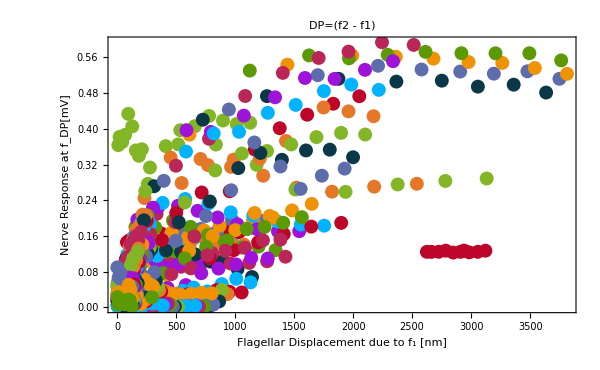

```mathematica
Show[{ListPlot[nThresholds,ImageSize->600,FrameLabel->{"Flagellar Displacement due to f_1 [nm]","Nerve Response at f_DP[mV]"},PlotLabel->"DP="<>dpChoiceN](*,Plot[Evaluate[#[x]&/@nFits],{x,-300,5000}]*)}]
```

```mathematica
Manipulate[Show[{ListPlot[nThresholds[[i]],PlotRange->{{-1000,4000},{-0.1,0.7}},PlotLabel->"f_1="<>ToString[freqROI[[i]]]<>" Hz\n f_DP = |"<>ToString[dpChoiceN]<>"| = "<>ToString[Abs@ToExpression[StringReplace[dpChoiceN,{"f2"->"540","f1"->ToString@freqROI[[i]]}]]]<>" Hz"],Plot[nFits[[i]][x],{x,-300,4000}]},FrameLabel->{"Flagellar Displacement due to f_1 [nm]","Nerve Response at f_DP[mV]"}],{i,1,Length@nFits,1},Paneled->False]
```

Part::partd: Part specification nThresholds[[1]]
     is longer than depth of object.

Part::partd: Part specification freqROI[[1]] is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

StringReplace::strse: 
   String or list of strings expected at position 1 in 
    StringReplace[dpChoiceN, {f2 -> 540, f1 -> freqROI[[1]]}].

ToExpression::notstrbox: 
   StringReplace[dpChoiceN, {f2 -> 540, f1 -> freqROI[[1]]}]
     is not a string or a box. ToExpression can only interpret strings or
     boxes as Wolfram Language input.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: nThresholds[[1]] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in 
    Show[{ListPlot[nThresholds[[1]], 
       PlotRange -> {{-1000, 4000}, {-0.1, 0.7}}, 
       PlotLabel -> f =freqROI[[1]] Hzf   = |dpChoiceN| = Abs[$Failed] Hz], 
                     1                 DP
      -Graphics-}, FrameLabel -> {<<3>>, <<3>>}].

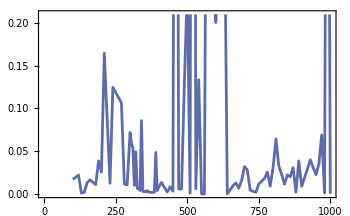

```mathematica
ListPlot[Table[{freqROI[[i]],Abs@k/.nFits[[i]]["BestFitParameters"]},{i,Range@Length@nFits}],PlotRange->Automatic,Joined->True]
```

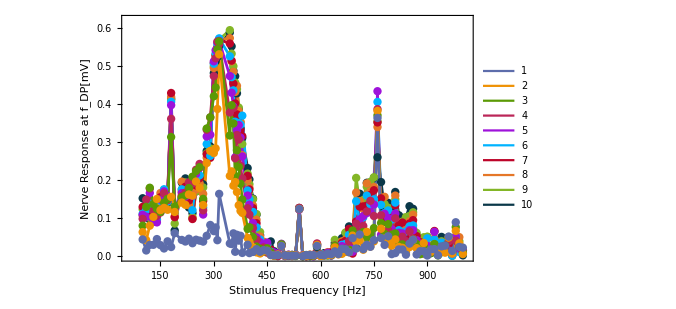

```mathematica
Show[{ListLinePlot[Reverse@({freqROI,nThresholds[[;;,#,2]]}ᵀ&/@Range[Length@nThresholds[[1]]]),PlotStyle->Reverse@cols,Frame->True,PlotLegends->LineLegend[cols,Range[Length@nThresholds[[1]]]]
,FrameLabel->{{"Nerve Response at f_DP[mV]",""},{"Stimulus Frequency [Hz]","DP Frequency [Hz]"}},PlotRange->{{60,1010},{0,0.62}},FrameTicks->{{Automatic,None},{Automatic,{Range[200,1000,200],Abs[540-Range[200,1000,200]]}ᵀ}},ImageSize->500,FrameStyle->Directive
[FontSize->18,AbsoluteThickness[2]]],
ListPlot[Reverse@({freqROI,nThresholds[[;;,#,2]]}ᵀ&/@Range[Length@nThresholds[[1]]]),PlotStyle->{AbsolutePointSize[6]&/@Range[10], Reverse@cols[[;;10]]}ᵀ]}]
```

```mathematica
Manipulate[Grid[{MapThread[ListPlot[{{freqROI,nThresholds[[;;,stimIntensity,#1]]}ᵀ},FrameLabel->{"Stimulus Frequency [Hz]",#2}]&,{{1,2},
{"Flagellar Displacement due to f_1 [nm]","Nerve Response at f_DP[mV]"},
{{darkBlue,orange2,Gray},{green2,orange,Gray}},{"Flagellar response","Nerve response"}}
](*MapThread end*)
}](*grid end*),

{{stimIntensity,2,"Stimulus Intensity"},1,Length@nThresholds[[1]],1},Paneled->False]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{100,110,120,130,140,160,200,210,220,240,«81»},{}} cannot be transposed.

Transpose::nmtx: The first two levels of {{100.,110.,120.,130.,140.,160.,200.,210.,220.,240.,«81»},{}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
Manipulate[Grid[{MapThread[Show[{ListLinePlot[{{freqROI,nThresholds[[;;,stimIntensity,#1]]}ᵀ,{freqROI,nThresholdsSSO[[;;,stimIntensity,#1]]}ᵀ,Sort[Table[{freqROI[[i]],nervePSThreshold[freqROI[[i]]][[#1,2]]},{i,Length@freqROI}]]},FrameLabel->{"Stimulus Frequency [Hz]",#2},PlotStyle->#3,PlotLegends->{#4,"SSO during stimulus","SSO prior to stimulus"}(*,PlotRange->{0,#5}*),Filling->{1->Bottom,2->None,3->None}],

ListPlot[{{freqROI,nThresholds[[;;,stimIntensity,#1]]}ᵀ,{freqROI,nThresholdsSSO[[;;,stimIntensity,#1]]}ᵀ,Sort[Table[{freqROI[[i]],nervePSThreshold[freqROI[[i]]][[#1,2]]},{i,Length@freqROI}]]},PlotStyle->{AbsolutePointSize[6]&/@Range[3],#3}ᵀ]}]&,{{1,2},
{"Flagellar Displacement due to f_1 [nm]","Nerve Response at f_DP[mV]"},
{{darkBlue,orange,Gray},{green,orange2,Gray}},{"Flagellar response","Nerve response"},{4000,0.6}}
](*MapThread end*)
}](*grid end*),

{{stimIntensity,2,"Stimulus Intensity"},1,Length@nThresholds[[1]],1},Paneled->False]
```

Transpose::nmtx: The first two levels of {{100,120,130,140,150,160,180,190,200,210,«84»},{}} cannot be transposed.

Transpose::nmtx: The first two levels of {{100.,120.,130.,140.,150.,160.,180.,190.,200.,210.,«84»},{}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLinePlot::lpn: {{},{},{{100.,158.123},{120.,157.372},{130.,157.275},{140.,154.543},{150.,156.455},{160.,157.164},{180.,153.653},{190.,151.811},{200.,152.718},{210.,155.167},«84»}} is not a list of numbers or pairs of numbers.

ListPlot::lpn: {{},{},{{100.,158.123},{120.,157.372},{130.,157.275},{140.,154.543},{150.,156.455},{160.,157.164},{180.,153.653},{190.,151.811},{200.,152.718},{210.,155.167},«84»}} is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[{Transpose[{{100,120,130,140,150,160,180,190,200,210,«84»},{}}],Transpose[{{100,120,130,140,150,160,180,190,200,210,«84»},{}}],{{100,158.123},{120,157.372},{130,157.275},{140,154.543},{150,156.455},{160,157.164},{180,153.653},{190,151.811},{200,152.718},{210,155.167},«84»}},FrameLabel→{Stimulus Frequency [Hz],Flagellar Displacement due to f_1 [nm]},PlotStyle→{color,color,color},PlotLegends→{Flagellar response,SSO during stimulus,SSO prior to stimulus},Filling→{1→Bottom,2→None,3→None}],ListPlot[{«1»},«9»→«1»]}].

ListLinePlot::lpn: {{},{},{{100.,0.0475179},{120.,0.0347124},{130.,0.0500533},{140.,0.0488597},{150.,0.0543028},{160.,0.0539395},{180.,0.0456203},{190.,0.0498803},{200.,0.0534735},{210.,0.0502691},«84»}} is not a list of numbers or pairs of numbers.

ListPlot::lpn: {{},{},{{100.,0.0475179},{120.,0.0347124},{130.,0.0500533},{140.,0.0488597},{150.,0.0543028},{160.,0.0539395},{180.,0.0456203},{190.,0.0498803},{200.,0.0534735},{210.,0.0502691},«84»}} is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[{Transpose[{{100,120,130,140,150,160,180,190,200,210,«84»},{}}],Transpose[{{100,120,130,140,150,160,180,190,200,210,«84»},{}}],{{100,0.0475179},{120,0.0347124},{130,0.0500533},{140,0.0488597},{150,0.0543028},{160,0.0539395},{180,0.0456203},{190,0.0498803},{200,0.0534735},{210,0.0502691},«84»}},FrameLabel→{Stimulus Frequency [Hz],Nerve Response at f_DP[mV]},PlotStyle→{color,color,color},PlotLegends→{Nerve response,SSO during stimulus,SSO prior to stimulus},Filling→{1→Bottom,2→None,3→None}],ListPlot[{«1»},«9»→«1»]}].

Transpose::nmtx: The first two levels of {{100,110,120,130,140,160,200,210,220,240,«81»},{}} cannot be transposed.

Transpose::nmtx: The first two levels of {{100.,110.,120.,130.,140.,160.,200.,210.,220.,240.,«81»},{}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLinePlot::lpn: {{},{},{{100.,205.981},{110.,205.303},{120.,205.32},{130.,208.094},{140.,206.801},{160.,202.72},{200.,201.889},{210.,203.305},{220.,201.6},{240.,190.843},«81»}} is not a list of numbers or pairs of numbers.

ListPlot::lpn: {{},{},{{100.,205.981},{110.,205.303},{120.,205.32},{130.,208.094},{140.,206.801},{160.,202.72},{200.,201.889},{210.,203.305},{220.,201.6},{240.,190.843},«81»}} is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[{Transpose[{{100,110,120,130,140,160,200,210,220,240,«81»},{}}],Transpose[{{100,110,120,130,140,160,200,210,220,240,«81»},{}}],{{100,205.981},{110,205.303},{120,205.32},{130,208.094},{140,206.801},{160,202.72},{200,201.889},{210,203.305},{220,201.6},{240,190.843},«81»}},FrameLabel→{Stimulus Frequency [Hz],Flagellar Displacement due to f_1 [nm]},PlotStyle→{color,color,color},PlotLegends→{Flagellar response,SSO during stimulus,SSO prior to stimulus},Filling→{1→Bottom,2→None,3→None}],ListPlot[{«1»},«1»]}].

ListLinePlot::lpn: {{},{},{{100.,0.00869999},{110.,0.00505912},{120.,0.00312999},{130.,0.0149827},{140.,0.00457686},{160.,0.00278699},{200.,0.0014849},{210.,0.00871601},{220.,0.00536538},{240.,0.0121957},«81»}} is not a list of numbers or pairs of numbers.

ListPlot::lpn: {{},{},{{100.,0.00869999},{110.,0.00505912},{120.,0.00312999},{130.,0.0149827},{140.,0.00457686},{160.,0.00278699},{200.,0.0014849},{210.,0.00871601},{220.,0.00536538},{240.,0.0121957},«81»}} is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[{Transpose[{{100,110,120,130,140,160,200,210,220,240,«81»},{}}],Transpose[{{100,110,120,130,140,160,200,210,220,240,«81»},{}}],{{100,0.00869999},{110,0.00505912},{120,0.00312999},{130,0.0149827},{140,0.00457686},{160,0.00278699},{200,0.0014849},{210,0.00871601},{220,0.00536538},{240,0.0121957},«81»}},FrameLabel→{Stimulus Frequency [Hz],Nerve Response at f_DP[mV]},PlotStyle→{color,color,color},PlotLegends→{Nerve response,SSO during stimulus,SSO prior to stimulus},Filling→{1→Bottom,2→None,3→None}],«1»}].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListLinePlot::lpn: 
   {{{1., freqROI}, {2., Symbol[]}}, {{1., freqROI}, {2., Symbol[]}}, {}}
     is not a list of numbers or pairs of numbers.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx
     will be suppressed during this calculation.

ListPlot::lpn: {{{1., freqROI}, {2., Symbol[]}}, 
     {{1., freqROI}, {2., Symbol[]}}, {}} is not a list of numbers or pairs of
     numbers.

Show::gcomb: Could not combine the graphics objects in 
    Show[{ListLinePlot[{{freqROI, Symbol[]}, {freqROI, Symbol[]}, {}}, 
       FrameLabel -> {Stimulus Frequency [Hz], F<<27>>o <<2>>}, <<2>>, 
       Filling -> {1 -> Bottom, 2 -> None, 3 -> None}], <<1>>}].

ListLinePlot::lpn: 
   {{{1., freqROI}, {2., Symbol[]}}, {{1., freqROI}, {2., Symbol[]}}, {}}
     is not a list of numbers or pairs of numbers.

ListPlot::lpn: {{{1., freqROI}, {2., Symbol[]}}, 
     {{1., freqROI}, {2., Symbol[]}}, {}} is not a list of numbers or pairs of
     numbers.

Show::gcomb: Could not combine the graphics objects in 
    Show[{ListLinePlot[{{freqROI, Symbol[]}, {freqROI, Symbol[]}, {}}, 
       FrameLabel -> {Stimulus Frequency [Hz], N<<15>>t <<2>>}, <<2>>, 
       Filling -> {1 -> Bottom, 2 -> None, 3 -> None}], <<1>>}].

{340,540,360.}

200

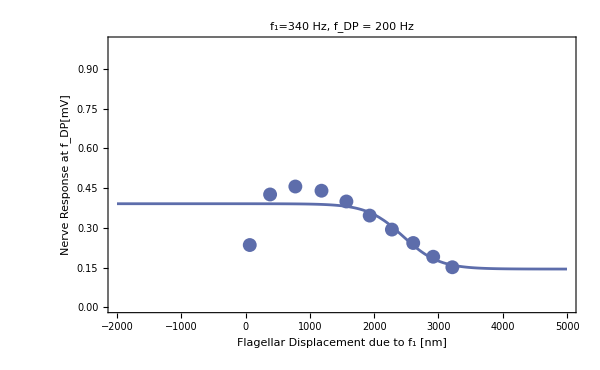

```mathematica
freqDesired=340;
chunkSize=4000;
{f1,f2,f3}=
{freqDesired,540,Reverse[SortBy[Select[fourier[fLaser[[Position[freqs,freqDesired][[1,1]],;;0.1 sRate]],sRate,800],300<=#[[1]]<=500&],Last]][[1,1]]} (* the experimental frequencies*)
fDP =(f2-f1) (* The DP frequency we want to track *)

satData=Table[{Select[fourier[fLaser[[Position[freqs,(*540-*)freqDesired][[1,1]],i;;i+chunkSize]],sRate,1200],#[[1]]==f1&][[1,2]],Select[fourier[fNerve[[Position[freqs,freqDesired][[1,1]],i;;i+2chunkSize]],sRate,1200],#[[1]]==fDP&][[1,2]]},{i,1,sRate*2,chunkSize}];

satFit=Quiet@NonlinearModelFit[satData[[;;]],A/(Exp[-k(x-x0)]+1)+c,{{A,Median[satData[[;;,2]]]},{k,10^-2},c,{x0,Median[satData[[;;,1]]]}},x];
Show[{Plot[satFit[x],{x,-2000,5000},PlotRange->(*{{0,200},*){0,1}(*}*)],
ListPlot[satData]},ImageSize->600,FrameLabel->{"Flagellar Displacement due to f_1 [nm]","Nerve Response at f_DP[mV]"},PlotLabel->"f_1="<>ToString[f1]<>" Hz, f_DP = "<>ToString[fDP]<>" Hz"]
```

What have other groups reported?
SIMOES ET AL 2016

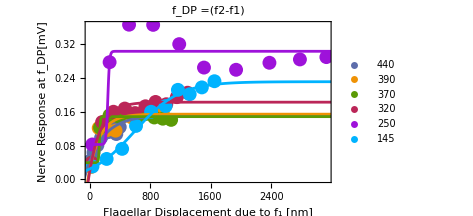

```mathematica
dpList=Round[Abs[540-{148,245.9,318,367.8,441,551,697}],5](*frequencies used in the Simoes et al 2016 paper*);
choices=Union[Sort[Position[Abs[freqROI-#],Min[Abs[freqROI-#]]][[1,1]]&/@dpList]];
Show[{ListPlot[nThresholds[[choices]](*,PlotRange->{{0,1000},Automatic}*),PlotLabel->"f_DP ="<>ToString[dpChoiceN],PlotLegends->540-freqROI[[choices]]],
Plot[Evaluate[nFits[[ #]][x]&/@ choices],{x,-300,4000}]},FrameLabel->{"Flagellar Displacement due to f_1 [nm]","Nerve Response at f_DP[mV]"}]
```

```mathematica
choiceRules=Normal[AssociationThread[{F1,F2},Coefficient[ToExpression[dpChoiceN],{f1,f2},1]]]; (* this just finds the coefficients of the chosen DP that we are tracking *)
choices=Flatten[Position[freqROI,#]&/@Select[freqROI,100<=F1#+F2 540<=240/.choiceRules&]]; (* this finds which stimulus frequencies lead to DPs RESPONSES (the Y AXIS!!!) that fall in the desired region of 100-240 Hz.*)
Show[{
Plot[Evaluate@Table[Callout[nFits[[choices[[i]]]][x],(*"f1 = "<>*)ToString[freqROI[[choices[[i]]]]]<>" Hz →" (*<>"fDP = "*)<>ToString[Evaluate[F1 freqROI[[choices[[i]]]]+F2 540/.choiceRules]]<>" Hz",Appearance->"Corners",
CalloutStyle->Directive@{cols[[Mod[i,Length@cols]]],Opacity[0.5]}],{i,Length@choices}],{x,-10,80},PlotRange->{0,0.7},ImageSize->600],
ListPlot[nThresholds[[choices]](*,PlotRange->{{0,1000},Automatic}*),PlotLabel->"f_DP ="<>ToString[dpChoiceN]]},FrameLabel->{"Flagellar Displacement due to f_1 [nm]","Nerve Response at f_DP[mV]"}]
```

-Graphics-

```mathematica
2f1-f2
2(2f1-f2)
```

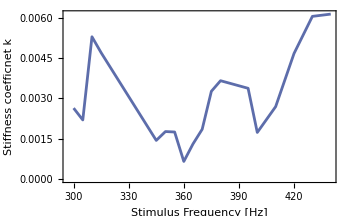

```mathematica
ListLinePlot[Table[{freqROI[[choices[[i]]]],Abs@k/.nFits[[choices[[i]]]]["BestFitParameters"]},{i,Range@Length@choices}],FrameLabel->{"Stimulus Frequency [Hz]","Stiffness coefficnet k"}]
```

### Firing rate (Kroese et al 1978)

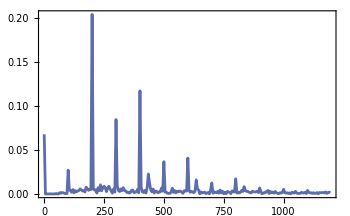

```mathematica
fourier[pNerv[[1,10]],sRate,1200]//ListLinePlot
```

### The sounds of violins and pianos

The purpose of this section is to see if there is a fundamental difference between the nerve responses for various DPs.
We already have proof that DPs are more sensitive than pure tones, but why? Perhaps the waveform plays a role.
Work with Mosquito 32 set 1

```mathematica
Values[Flatten[commonFreqs]]
```

{180,90,360,360,720,900}

```mathematica
dFreq=200; (* desired frequency *)
DPsofInterest={f1,2f1,f2-f1,2f1-f2,f1-f2,2f2-f1};
commonFreqs=Flatten[Solve[#==dFreq,f1]&/@(DPsofInterest/.{f2->540}) ](* finds the frequencies that generate a DP of dFreq *)
commonPos=Flatten[Position[freqs,#]&/@Values[Flatten[commonFreqs]]] (* finds where these frequencies are in the list of frequencies for this experiment*)
```

{f1→200,f1→100,f1→340,f1→370,f1→740,f1→880}

{7,1,21,27,65,79}

```mathematica
Clear[myticks]
tickF[t1_:{0.,.02},t2_:{0.,.01}]:=Replace[Charting`FindTicks[{0,1},{0,1}][##],{{t_?NumericQ,l_?NumericQ}:>{t,l,t1},{t_,"",_,c___}:>{t,"",t2,c}},1]&;
```

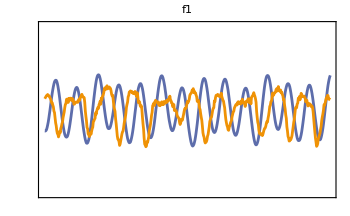
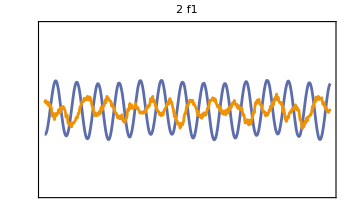
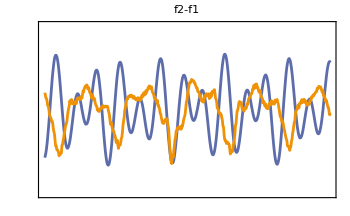
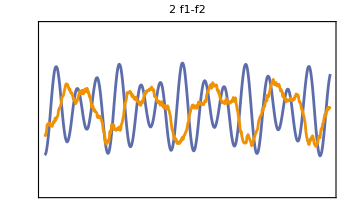
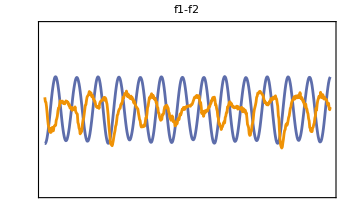
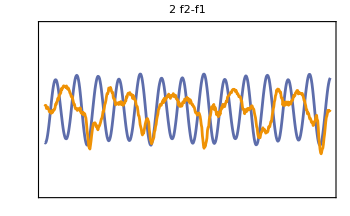

```mathematica
st=1;
seg=5;
ListLinePlot[{0.2 10^-3 pLaser[[commonPos[[#]],seg]][[st;;st+500]],pNerv[[commonPos[[#]],seg]][[st;;st+500]]},PlotRange->1.5{-1,1},PlotLabel->DPsofInterest[[#]],Axes->False,Frame->True,FrameTicks->None]&/@Range@Length@commonPos
```

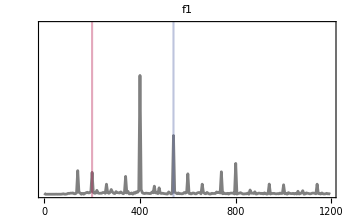
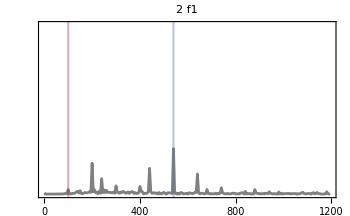
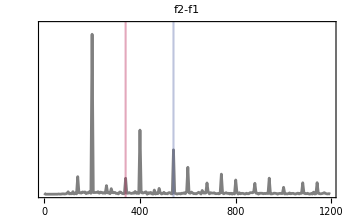
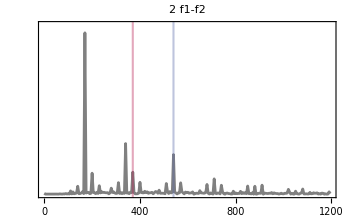
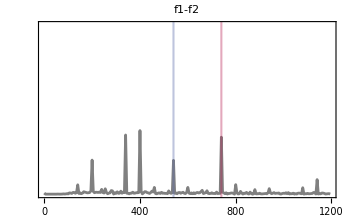
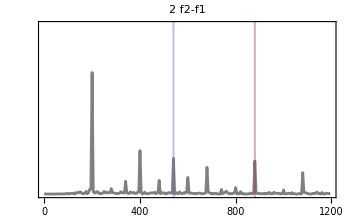

```mathematica
tk=Table[{i,i,{0,0.015}},{i,0,1200,200}];
ListLinePlot[fourier[pNerv[[commonPos[[#]],seg]][[st;;]],sRate,1200],Frame->{True,False,False,False},PlotRange->{0,0.42},PlotLabel->DPsofInterest[[#]],GridLines->{{{Values[commonFreqs][[#]],Directive[pink,AbsoluteThickness[1.5]]},{540,Directive[blue,AbsoluteThickness[1.5]]}},None},FrameStyle->{Black,AbsoluteThickness[1]},FrameTicks->{tk,None},FrameTicksStyle->20,PlotStyle->{Gray,AbsolutePointSize[2]}]&/@Range@Length@commonPos
```

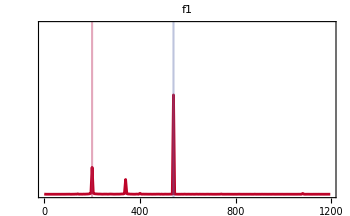
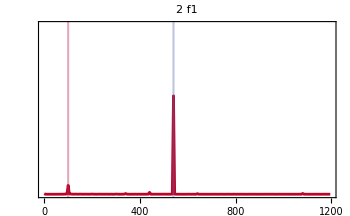
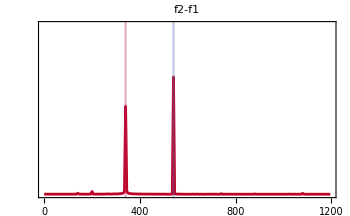
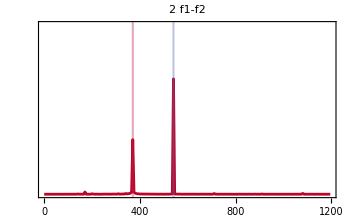
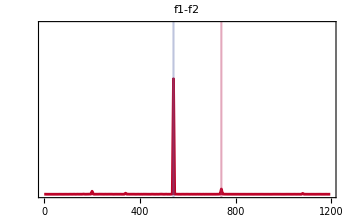
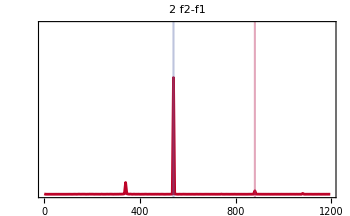

```mathematica
ListLinePlot[MapAt[10^-4#&,fourier[pLaser[[commonPos[[#]],seg]][[st;;]],sRate,1200],{All,2}],Frame->{True,False,False,False},PlotRange->{0,0.42},PlotLabel->DPsofInterest[[#]],GridLines->{{{Values[commonFreqs][[#]],Directive[pink,AbsoluteThickness[1.5]]},{540,Directive[blue,AbsoluteThickness[1.5]]}},None},FrameStyle->{Black,AbsoluteThickness[1]},FrameTicks->{tk,None},FrameTicksStyle->20,PlotStyle->{red,AbsolutePointSize[2]}]&/@Range@Length@commonPos
```

If we were to bandpass the data to the “biologically relevant region” of 0-500 Hz, would the nerve look essentially the same or not?
Will the stream analysis be better off with such a filter?

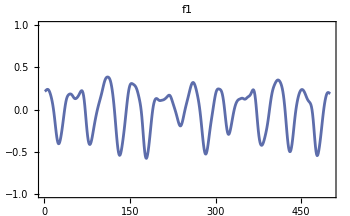
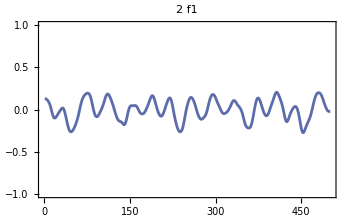
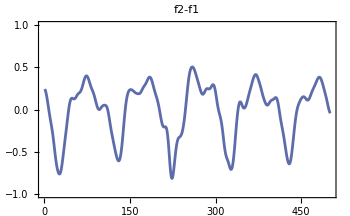
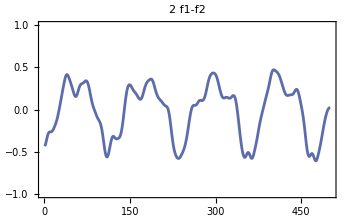
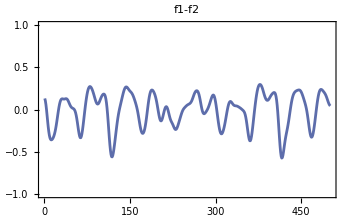
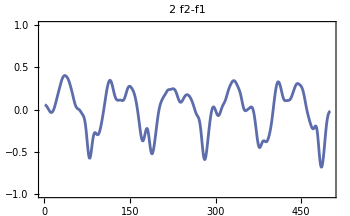

```mathematica
ListLinePlot[Fold[LowpassFilter,pNerv[[commonPos[[#]],5]][[st;;st+500]],2π/sRate Table[2500,{i,4}]],PlotRange->{-1,1},PlotLabel->DPsofInterest[[#]]]&/@Range@Length@commonPos
```

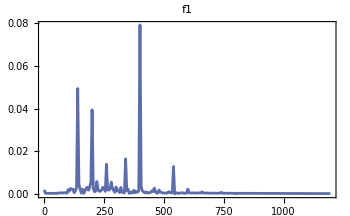
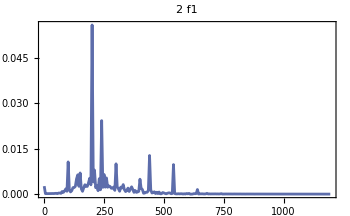
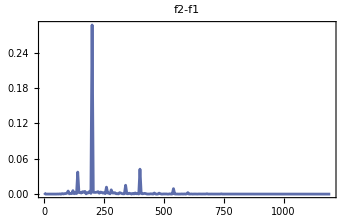
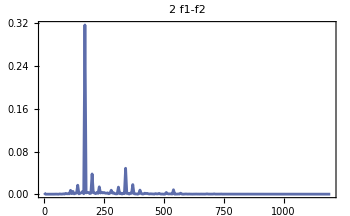
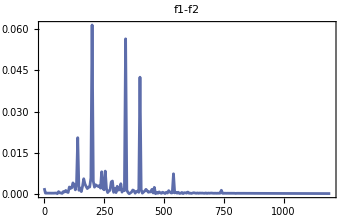
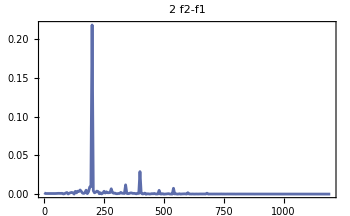

```mathematica
ListLinePlot[fourier[Fold[LowpassFilter,pNerv[[commonPos[[#]],5]][[st;;]],2π/sRate{500,500,500,500}],sRate,1200],PlotRange->Full,PlotLabel->DPsofInterest[[#]]]&/@Range@Length@commonPos
```

```mathematica
ListPlay[Flatten[Table[pNerv[[commonPos[[#]],5]],{i,5}]],SampleRate->sRate]&/@Range@Length@commonPos
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
220/20.
```

11.

```mathematica
321/38.
```

8.44737

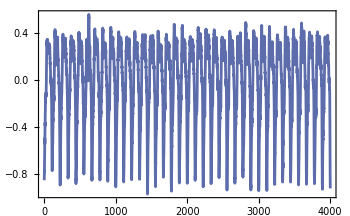
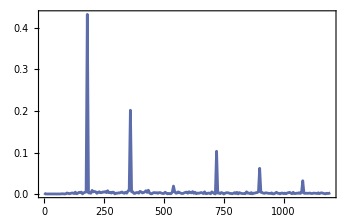

```mathematica
{ListLinePlot[pNerv[[25,3]]],ListLinePlot[fourier[pNerv[[25,3]],sRate,1200]]}
```

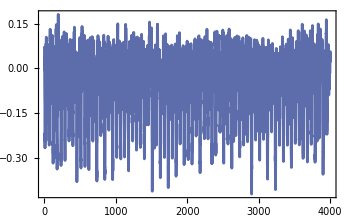
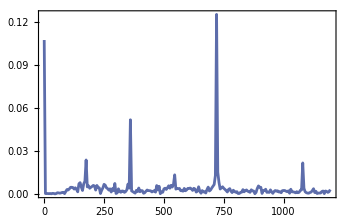

```mathematica
test=Fold[HighpassFilter,readMyFile[nervefiles1T[[31]]][[;;,2]],2π/sRate{60,60,60}][[12000;;16000]];
{ListLinePlot[test],ListLinePlot[fourier[test,sRate,1200]]}
```

```mathematica
test=Fold[HighpassFilter,readMyFile[nervefiles1T[[31]]][[;;,2]],2π/sRate{60,60,60}][[12000;;16000]];
{ListLinePlot[test],ListLinePlot[fourier[test,sRate,1200]]}
```

```mathematica
Position[freqs1T,170]
```

{{8}}

#### What happens if you want to kill the higher frequency response frequencies?

Many of the features of the compound action potentials start to vanish once you start removing frequencies above 1200 Hz. At 800 Hz LPF you have lost almost all features and are left with 
just a barebone signal.

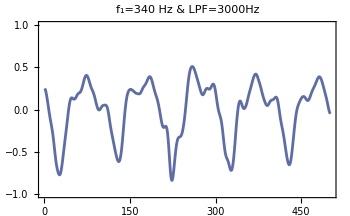
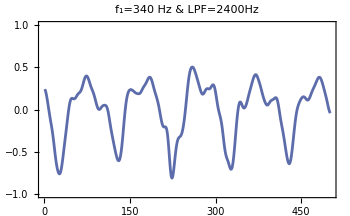
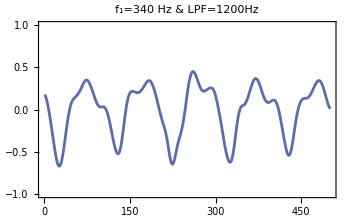
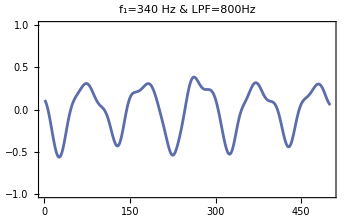
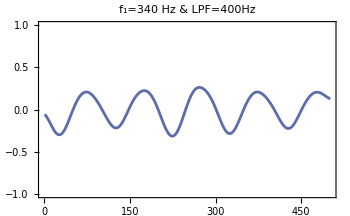

```mathematica
ListLinePlot[Fold[LowpassFilter,pNerv[[21,5]][[st;;st+500]],2π/sRate Table[#,{i,4}]],PlotLabel->"f_1=340 Hz & LPF="<>ToString[#]<>"Hz",PlotRange->{-1,1}]&/@Reverse@{400,800,1200,2400,3000}
```